```mathematica
$HistoryLength=0;
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Print["Byte ordering su questa macchina: ",$ByteOrdering];
```

Byte ordering su questa macchina: -1

## Display dei risultati della simulazione

### Lettura del file

```mathematica
dir= "/localdisk/thierry/output_milotti/runs/"; 
RunNumber="run_34-name";
```

```mathematica
BO = $ByteOrdering; (* qui si definisce il ByteOrdering del file rispetto quello della macchina attuale *)
```

```mathematica
RecordNumberMin=55; (* record iniziale *)
RecordNumberMax = 55; (* record finale; NB: se RecordNumberMax è minore di RecordNumberMin, vengono letti tutti i records a partire da RecordNumberMin *)
RecordStep = 1; (* passo di lettura dei records *)

t = {};
ncells = {};
EnvVolume = {};
GenvConc = {};
O2envConc = {};
AenvConc = {};
AcLenvConc = {};
x={};
v={};
links={};
isonCH ={};
isonAS ={};
r = {};
phase = {};
G = {};
Gextra = {};
GAbsRate = {};
GConsRate = {};
G6P = {};
O2 = {};
Store = {};
A = {};
Aextra = {};
AAbsRate = {};
AConsRate = {};
AcL = {};
AcLextra = {};
ATPp = {};
Mit = {};
pH = {};
protein = {};
protRate = {};
pRb = {};
ConcS = {};
DNArate = {};
age = {};
phaseage={};

fO2 = {};
fG = {};
fA = {};
fAcL = {};

RecordNumber = RecordNumberMin;

While[ ToString[(stream=Quiet[OpenRead[dir<>RunNumber<>"/configuration_b/"<>ToString[RecordNumber]<>".bin",BinaryFormat->True]])] != ToString[$Failed]  && (RecordNumber ≤ RecordNumberMax || RecordNumberMin > RecordNumberMax),

SimType = BinaryRead[stream,"Integer32", ByteOrdering->BO];
(* Which[SimType==0,Print["Simulazione con cellule disperse"];Visualize=False,
SimType==1,Print["Simulazione Full3D"];Visualize=True,
SimType==2,Print["Simulazione con configurazione fissa"];Visualize=True]; *)


step = BinaryRead[stream,"Integer64", ByteOrdering->BO];
treal = BinaryRead[stream,"Real64", ByteOrdering->BO];
ncell = BinaryRead[stream,"Integer64", ByteOrdering->BO];
AppendTo[ncells,ncell];

PrintTemporary["Record "<>ToString[RecordNumber]<>" has "<>ToString[ncell]<>" cells"];

EnvVolumenow = BinaryRead[stream,"Real64", ByteOrdering->BO];
GenvConcnow = BinaryRead[stream,"Real64", ByteOrdering->BO];
O2envConcnow = BinaryRead[stream,"Real64", ByteOrdering->BO];
AenvConcnow = BinaryRead[stream,"Real64", ByteOrdering->BO];
AcLenvConcnow = BinaryRead[stream,"Real64", ByteOrdering->BO];

xs=vs=Table[{},{ncell}];
For[j=1,j≤ncell,
xs[[j]]=BinaryRead[stream,{"Real64","Real64","Real64"}, ByteOrdering->BO];
vs[[j]]=BinaryRead[stream,{"Real64","Real64","Real64"}, ByteOrdering->BO];
j++];

linkstemp=Table[{},{ncell}];
For[j=1,j≤ncell,
nlinks=BinaryRead[stream,"Integer32", ByteOrdering->BO];
If[nlinks>0,linkstemp[[j]] =BinaryRead[stream,Table["Integer32",{nlinks}], ByteOrdering->BO] ];
j++];

isonCHnow =  BinaryRead[stream,Table["Byte",{ncell}], ByteOrdering->BO];
isonASnow =  BinaryRead[stream,Table["Byte",{ncell}], ByteOrdering->BO];
rnow =  BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO]; (* conversione in micron !!! *)
phasenow =  BinaryRead[stream,Table["Integer32",{ncell}], ByteOrdering->BO];
Gnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
Gextranow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
GAbsRatenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
GConsRatenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
G6Pnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
O2now = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
Storenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
Anow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
Aextranow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
AAbsRatenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
AConsRatenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
AcLnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
AcLextranow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
ATPpnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
Mitnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
pHnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
proteinnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
protRatenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
pRbnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
ConcSnow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
DNAratenow = BinaryRead[stream,Table["Real64",{ncell}], ByteOrdering->BO];
agenow = BinaryRead[stream,Table["Real32",{ncell}], ByteOrdering->BO];
phaseagenow = BinaryRead[stream,Table["Real32",{ncell}], ByteOrdering->BO];

AppendTo[t,treal];

AppendTo[EnvVolume,EnvVolumenow];
AppendTo[GenvConc,GenvConcnow];
AppendTo[O2envConc,O2envConcnow];
AppendTo[AenvConc,AenvConcnow];
AppendTo[AcLenvConc,AcLenvConcnow];

AppendTo[x,xs];
AppendTo[v,vs];
AppendTo[links,linkstemp];
AppendTo[isonCH , isonCHnow ];
AppendTo[isonAS , isonASnow ];
AppendTo[r ,  rnow];
AppendTo[phase , phasenow ];
AppendTo[G ,Gnow ];
AppendTo[Gextra ,Gextranow ];
AppendTo[GAbsRate ,GAbsRatenow ];
AppendTo[GConsRate ,GConsRatenow ];
AppendTo[G6P,G6Pnow ];
AppendTo[O2 ,O2now ];
AppendTo[Store ,Storenow ];
AppendTo[A ,Anow ];
AppendTo[Aextra,Aextranow ];
AppendTo[AAbsRate ,AAbsRatenow ];
AppendTo[AConsRate ,AConsRatenow ];
AppendTo[AcL ,AcLnow ];
AppendTo[AcLextra , AcLextranow ];
AppendTo[ATPp ,ATPpnow ];
AppendTo[Mit ,Mitnow ];
AppendTo[pH ,pHnow ];
AppendTo[protein ,proteinnow];
AppendTo[protRate,protRatenow];
AppendTo[pRb,pRbnow];
AppendTo[ConcS,ConcSnow];
AppendTo[DNArate,DNAratenow];
AppendTo[age,agenow];
AppendTo[phaseage,phaseagenow];


Close[stream];

stream=OpenRead[dir<>RunNumber<>"/flows_b/"<>ToString[RecordNumber]<>".bin",BinaryFormat->True];

fO2now=fGnow=fAnow=fAcLnow=Table[{},{ncell}];

For[j=1,j≤ncell, 

fO2now[[j]]=BinaryRead[stream,Table["Real64",{3}], ByteOrdering->BO];
fGnow[[j]]=BinaryRead[stream,Table["Real64",{3}], ByteOrdering->BO];
fAnow[[j]]=BinaryRead[stream,Table["Real64",{3}], ByteOrdering->BO];
fAcLnow[[j]]=BinaryRead[stream,Table["Real64",{3}], ByteOrdering->BO];

j++];

AppendTo[fO2,fO2now];
AppendTo[fG,fGnow];
AppendTo[fA,fAnow];
AppendTo[fAcL,fAcLnow];

Close[stream];

RecordNumber+=RecordStep;

];

maxstep=Length[x];
Print["There are ",maxstep," simulation steps"];

volume=4*Pi*r[[maxstep]]^3 /3;
surface = 4*Pi*r[[maxstep]]^2;
volumeextra = surface * 0.1;
centroid=Apply[Plus,(x[[maxstep]] volume)]/Apply[Plus,( volume)];
maxdist=Max[Table[Abs[x[[maxstep,k]]-centroid],{k,1,Length[x[[maxstep]]]}]]+2*Max[r];
Print["Centroid of cell distribution is ",centroid];
```

There are 1 simulation steps

Centroid of cell distribution is {-3.73732,-3.85373,5.91133}

### Calcoli per definire il range di posizione

```mathematica
xt=Transpose[x[[maxstep]]];
minX=Min[xt[[1]]];
maxX=Max[xt[[1]]];
minY=Min[xt[[2]]];
maxY=Max[xt[[2]]];
minZ=Min[xt[[3]]];
maxZ=Max[xt[[3]]];
dX = maxX-minX;
dY = maxY-minY;
dZ = maxZ-minZ;
rangeX = {centroid[[1]]-dX,centroid[[1]]+dX};
rangeY = {centroid[[2]]-dY,centroid[[2]]+dY};
rangeZ = {centroid[[3]]-dZ,centroid[[3]]+dZ};

Print["Range X: ",rangeX];
Print["Range Y: ",rangeY];
Print["Range Z: ",rangeZ];
```

Range X: {-124.158,116.683}

Range Y: {-126.703,118.995}

Range Z: {-114.341,126.163}

```mathematica
ct=Table[0,{maxstep}];
For[nstep=1, nstep≤maxstep,

volume=4*Pi*r[[nstep]]^3 /3;
ct[[nstep]]=Apply[Plus,(x[[nstep]] volume)]/Apply[Plus,( volume)];

nstep++];

If[Length[x]>1,
ctt=Transpose[ct];
Print[Show[ListPlot[Transpose[{t,ctt[[1]]}],Joined->True,PlotStyle->AbsoluteThickness[2]],Plot[{minX,maxX},{tt,t[[1]],t[[maxstep]]}]]];
Print[Show[ListPlot[Transpose[{t,ctt[[2]]}],Joined->True,PlotStyle->AbsoluteThickness[2]],Plot[{minY,maxY},{tt,t[[1]],t[[maxstep]]}]]];
Print[Show[ListPlot[Transpose[{t,ctt[[3]]}],Joined->True,PlotStyle->AbsoluteThickness[2]],Plot[{minZ,maxZ},{tt,t[[1]],t[[maxstep]]}]]];
]
```

### Plot del numero di cellule

```mathematica
If[Length[x]>1,
Print[ListPlot[Transpose[{t,ncells}],PlotRange->All,Frame->True,Joined->True,PlotStyle->AbsoluteThickness[3],FrameStyle->18,ImageSize->8*72]];tfit=FindFit[Take[Transpose[{t,ncells}],{1,Floor[Length[t]/2]}],2^(tt/tau),{{tau,100000}},tt];Print[Show[ListLogPlot[Transpose[{t,ncells}],PlotRange->All,Frame->True,Joined->True,PlotStyle->AbsoluteThickness[3],FrameStyle->18,ImageSize->8*72],LogPlot[2^(tt/tau)/.tfit,{tt,0,Max[t]}]]];
Print["Tempo medio di duplicazione: ",tfit[[1,2]],"s = ",tfit[[1,2]]/3600,"h"];Print["assumendo che la crescita sia esponenziale"],Print["Numero di records insufficiente"]
]
```

Numero di records insufficiente

## Sections

### Statements da eseguire prima dei plots

```mathematica
zheight = 0; (* posizione della slice in micron *)

xpos = Table[x[[maxstep,k,1]]-ct[[maxstep,1]],{k,1,ncells[[maxstep]]}];
ypos = Table[x[[maxstep,k,2]]-ct[[maxstep,2]],{k,1,ncells[[maxstep]]}];
zpos = Table[x[[maxstep,k,3]]-ct[[maxstep,3]],{k,1,ncells[[maxstep]]}];

rpos =Table[Sqrt[xpos[[k]]^2+ypos[[k]]^2],{k,1,Length[xpos]}];

maxr = Max[rpos];

zmin = Min[zpos];
zmax = Max[zpos];

Print["zmin: ",zmin];
Print["zmax: ",zmax];

Print["max r: ",maxr];
```

zmin: -60.187

zmax: 60.0651

max r: 64.0508

```mathematica
slice={};
For[k=1,k≤ncells[[maxstep]],
If[Abs[zpos[[k]]-zheight]<r[[maxstep,k]],AppendTo[slice,k]];
k++];

Print["Cells in slice: ",Length[slice]];
```

Cells in slice: 217

```mathematica
For[k=1,k≤ncells[[maxstep]],
If[!NumberQ[Norm[v[[maxstep,k]]]],v[[maxstep,k]]={0,0,0}];
If[!NumberQ[Norm[fO2[[maxstep,k]]]],fO2[[maxstep,k]]={0,0,0}];
If[!NumberQ[Norm[fG[[maxstep,k]]]],fG[[maxstep,k]]={0,0,0}];
If[!NumberQ[Norm[fA[[maxstep,k]]]],fA[[maxstep,k]]={0,0,0}];
If[!NumberQ[Norm[fAcL[[maxstep,k]]]],fAcL[[maxstep,k]]={0,0,0}];
k++]
```

```mathematica
vslice=v[[maxstep,slice]];
fO2slice=fO2[[maxstep,slice]];
fGslice=fG[[maxstep,slice]];
fAslice=fA[[maxstep,slice]];
fAcLslice=fAcL[[maxstep,slice]];
```

### Display del convex hull

```mathematica
Apply[Plus,isonCH[[maxstep]]]
```

231

```mathematica
Show[Graphics3D[{AbsoluteThickness[2],
Line[{{-200,-200,-200},{-200,200,-200}}],
Line[{{-200,-200,200},{-200,200,200}}],
Line[{{-200,200,-200},{200,200,-200}}],
Line[{{-200,200,200},{200,200,200}}],
Line[{{-200,200,200},{-200,200,-200}}],
Line[{{200,200,200},{200,200,-200}}]}],
Graphics3D[Table[If[isonCH[[maxstep,k]]==1,Sphere[{xpos[[k]],ypos[[k]],zpos[[k]]},r[[maxstep,k]]],{}],{k,1,ncells[[maxstep]]}]],PlotRange->{{-200,200},{-200,200},{-200,200}},Boxed->False,Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesStyle->Directive[14,AbsoluteThickness[2]],FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}}]
```

-Graphics3D-

### Display dell' alpha shape

```mathematica
Apply[Plus,isonAS[[maxstep]]]
```

370

```mathematica
Show[Graphics3D[{AbsoluteThickness[2],
Line[{{-200,-200,-200},{-200,200,-200}}],
Line[{{-200,-200,200},{-200,200,200}}],
Line[{{-200,200,-200},{200,200,-200}}],
Line[{{-200,200,200},{200,200,200}}],
Line[{{-200,200,200},{-200,200,-200}}],
Line[{{200,200,200},{200,200,-200}}]}],
Graphics3D[Table[If[isonAS[[maxstep,k]]==1,Sphere[{xpos[[k]],ypos[[k]],zpos[[k]]},r[[maxstep,k]]],{}],{k,1,ncells[[maxstep]]}]],PlotRange->{{-200,200},{-200,200},{-200,200}},Boxed->False,Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesStyle->Directive[14,AbsoluteThickness[2]],FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}}]
```

-Graphics3D-

### Convex hull

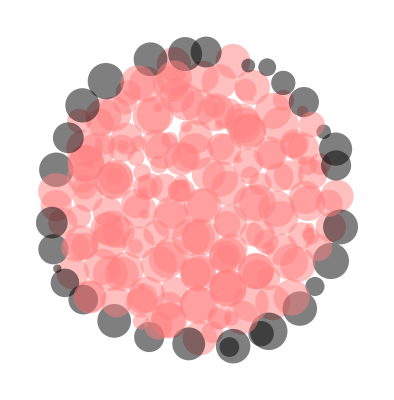

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{If[isonCH[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonCH[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

#### con effetto di sfuocatura

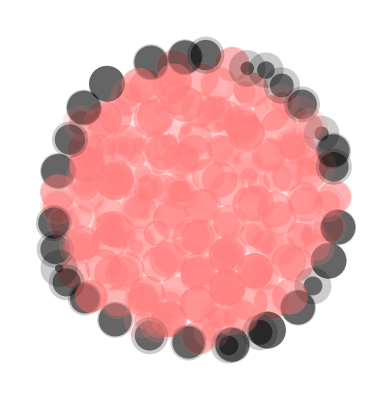

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{If[isonCH[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonCH[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{If[isonCH[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonCH[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Alpha shape

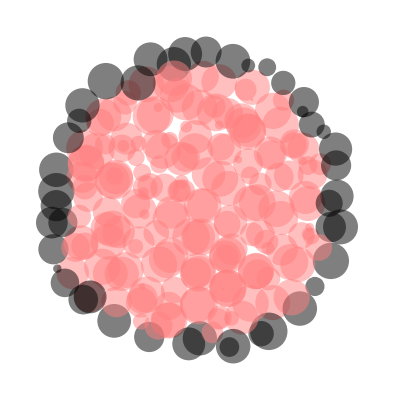

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{If[isonAS[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonAS[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

#### con effetto di sfuocatura

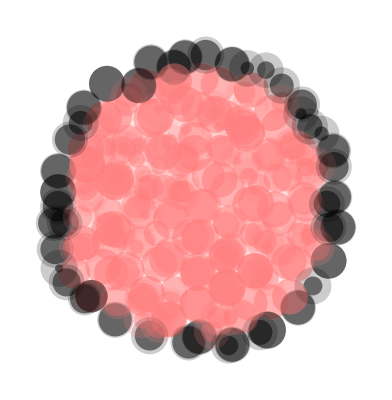

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{If[isonAS[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonAS[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{If[isonAS[[maxstep,slice[[k]]]] == 1,Black,RGBColor[1,0.5,0.5]],If[isonAS[[maxstep,slice[[k]]]] == 1,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Cellule morte

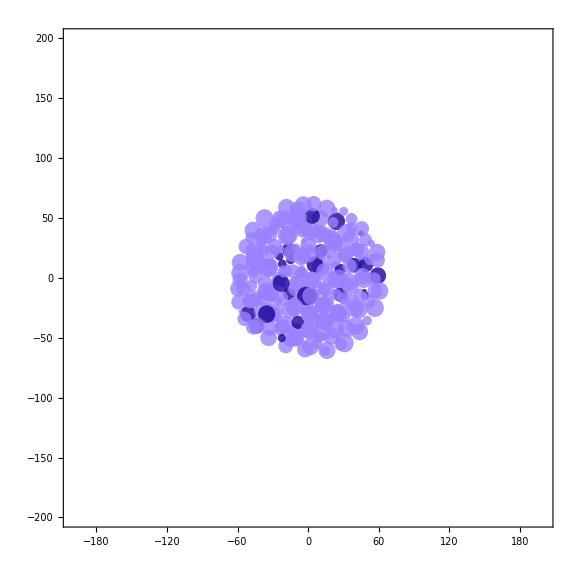

```mathematica
Print[Show[Graphics[{Opacity[0.8],Table[{If[phase[[maxstep,slice[[k]]]] == 6,RGBColor[0.1,0.,0.6],RGBColor[0.6,0.5,1.0]],If[phase[[maxstep,slice[[k]]]] == 6,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],
PlotRange->{{-200,200},{-200,200}},Frame->True,FrameStyle->Directive[14,Bold, FontFamily->"Arial",AbsoluteThickness[2]],ImageMargins->5,ImageSize->8*72]];
```

#### con effetto di sfuocatura

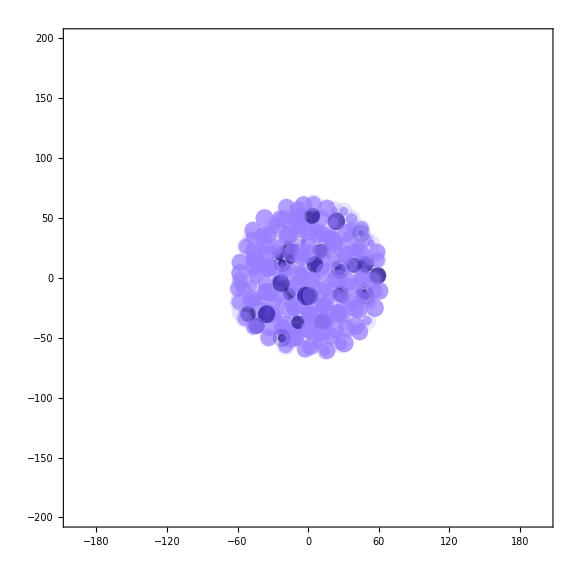

```mathematica
Print[Show[Graphics[{Opacity[0.7],Table[{If[phase[[maxstep,slice[[k]]]] == 6,RGBColor[0.05,0.,0.5],RGBColor[0.6,0.5,1.0]],If[phase[[maxstep,slice[[k]]]] == 6,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2]]]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{If[phase[[maxstep,slice[[k]]]] == 6,RGBColor[0.1,0.,0.6],RGBColor[0.6,0.5,1.0]],If[phase[[maxstep,slice[[k]]]] == 6,Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]]},{k,1,Length[slice]}]}],
PlotRange->{{-200,200},{-200,200}},Frame->True,FrameStyle->Directive[14,Bold, FontFamily->"Arial",AbsoluteThickness[2]],ImageMargins->5,ImageSize->8*72]];
```

### Età cellulari

```mathematica
ndead=Count[phase[[maxstep]],6]
```

136

```mathematica
nlive = ncells[[maxstep]]-ndead
```

1034

```mathematica
agelive=Table[0,{nlive}];
For[k=1; l=0,k<ncells[[maxstep]],
If[phase[[maxstep,k]]≠6,l++;agelive[[l]]=age[[maxstep,k]] ];
k++]
```

#### istogramma delle età cellulari delle cellule vive

```mathematica
Histogram[agelive,Frame->True,FrameStyle->18,ImageSize->8*72]
```

-Graphics-

```mathematica
Min[agelive]
```

-4.81035×10^36

```mathematica
Max[agelive]
```

3.64658×10^37

```mathematica
agemin = 1000000;
agemax = 0;
For[k=1,k≤Length[age[[maxstep,slice]]],
If[ phase[[maxstep,slice[[k]]]] ≠6,
agek=age[[maxstep,slice[[k]]]];
If[agek>agemax,agemax=agek];
If[agek<agemin,agemin=agek];
];
k++];

Print["Max age live cells ",agemax];
Print["Min age live cells ",agemin];
```

Max age live cells 3.64658×10^37

Min age live cells -5.1131×10^10

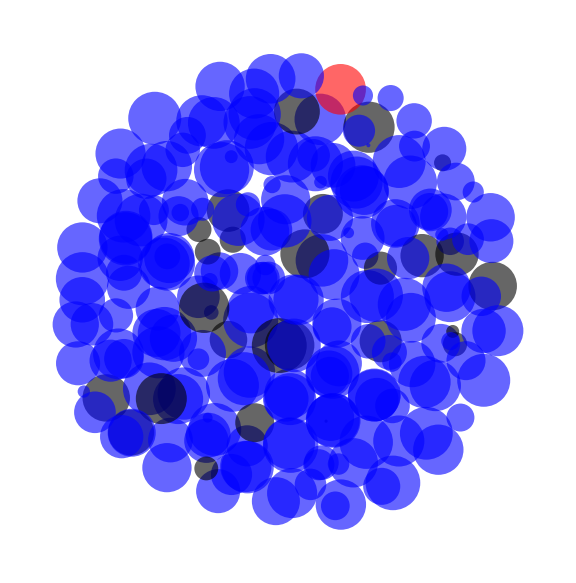

```mathematica
agemin=70000;Print[Show[Graphics[{Opacity[0.6],Table[{Which[ phase[[maxstep,slice[[k]]]] ≠6 && age[[maxstep,slice[[k]]]]>agemin,Red,phase[[maxstep,slice[[k]]]] ==6,Black,True,Blue],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
PlotRange->All,ImageSize->8*72]];
```

### Età cellulari (phase age)

Max phase age for G1 cells 3.64658×10^37

Min phase age for G1 cells -5.1131×10^10

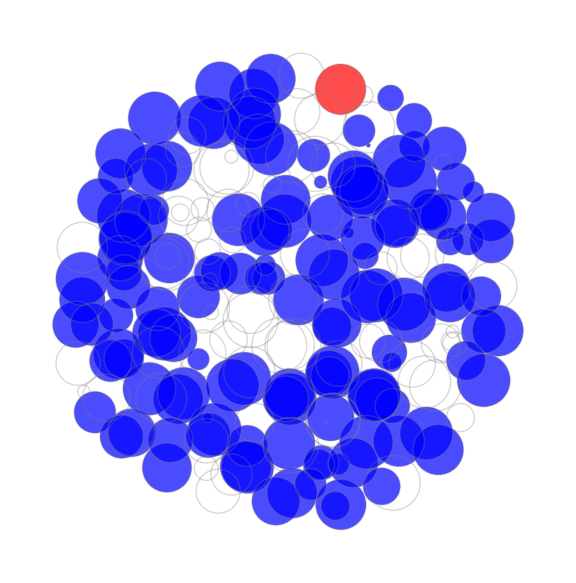

```mathematica
phaseagemin = 1000000;
phaseagemax = 0;
For[k=1,k≤Length[age[[maxstep,slice]]],
If[ phase[[maxstep,slice[[k]]]] ==1 || phase[[maxstep,slice[[k]]]] ==2 ,
phaseagek=age[[maxstep,slice[[k]]]];
If[phaseagek>phaseagemax,phaseagemax=phaseagek];
If[phaseagek<phaseagemin,phaseagemin=phaseagek];
];
k++];

Print["Max phase age for G1 cells ",phaseagemax];
Print["Min phase age for G1 cells ",phaseagemin];


Print[Show[Graphics[{Opacity[0.7],Table[{If[phase[[maxstep,slice[[k]]]]==1 || phase[[maxstep,slice[[k]]]]==2,{RGBColor[Min[1,(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)],0,  Min[1,1-(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{}]},{k,1,Length[slice]}]}],
Graphics[{Opacity[0.3],GrayLevel[0.5],Table[{Circle[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
PlotRange->All,ImageSize->8*72]];
```

#### con cellule morte

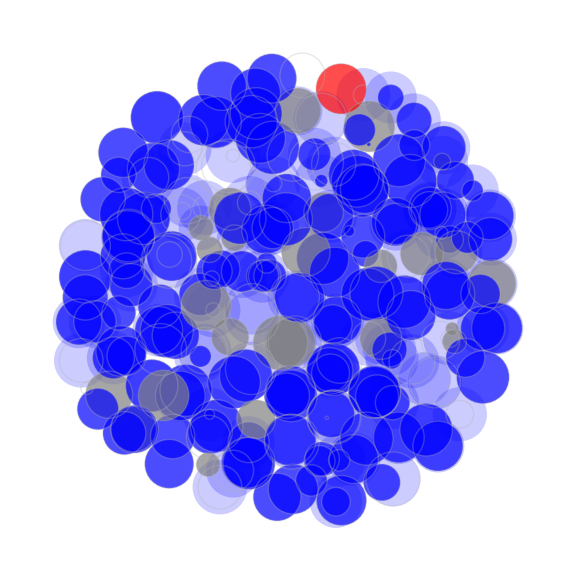

```mathematica
Print[Show[Graphics[{Opacity[0.2],Table[{If[phase[[maxstep,k]]==1 || phase[[maxstep,k]]==2,{RGBColor[Min[1,(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)],0,  Min[1,1-(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ]},{}]},{k,1,Length[slice]}]}],
Graphics[{Opacity[0.7],Table[{Which[phase[[maxstep,slice[[k]]]]==1 || phase[[maxstep,slice[[k]]]]==2,{RGBColor[Min[1,(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)],0,  Min[1,1-(age[[maxstep,slice[[k]]]]-phaseagemin)/(phaseagemax-phaseagemin)]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},
phase[[maxstep,slice[[k]]]]==6,{GrayLevel[0.5],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},
True,{}]},{k,1,Length[slice]}]}],
Graphics[{Opacity[0.3],GrayLevel[0.7],Table[{Circle[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
PlotRange->All,ImageSize->8*72]];
```

### Concentrazione di O2

Max O2 concentration 0.16964

Min O2 concentration 6.2332×10^-6

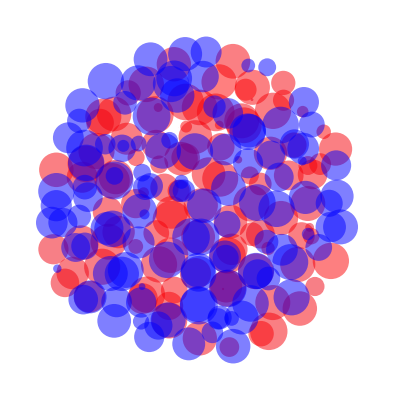

```mathematica
O2max =Max[O2[[maxstep,slice]]]; 
O2min =Min[O2[[maxstep,slice]]]; 

Print["Max O2 concentration ",O2max];
Print["Min O2 concentration ",O2min];


Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min),0,1-( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

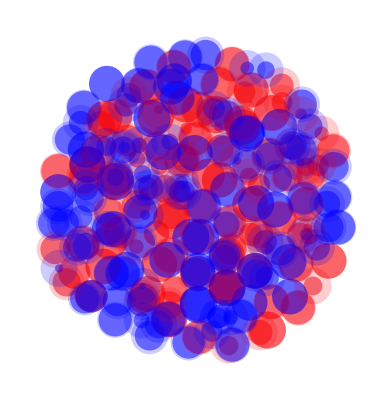

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min),0,1-( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ ( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min),0,1-( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Concentrazione del glucosio extracellulare

Max Gextra concentration 0.274629

Min Gextra concentration 0.00089738

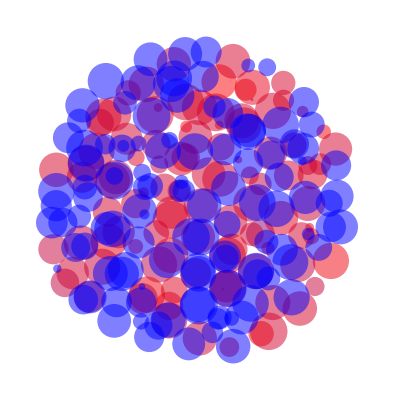

```mathematica
Gmax =Max[Gextra[[maxstep,slice]]]; 
Gmin=Min[Gextra[[maxstep,slice]]]; 

Print["Max Gextra concentration ",Gmax];
Print["Min Gextra concentration ",Gmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin),0,1-( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

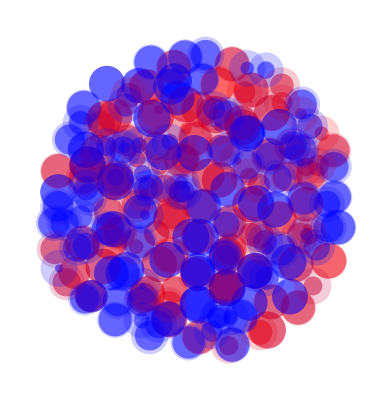

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin),0,1-( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
Graphics[{Opacity[0.2],Table[{RGBColor[ ( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin),0,1-( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Assorbimento di glucosio

Max GAbsRate 0.00151491

Min GAbsRate 0.000189384

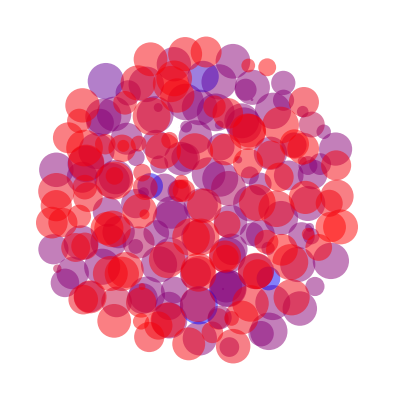

```mathematica
GAbsRatemax =Max[GAbsRate[[maxstep,slice]]]; 
GAbsRatemin =Min[GAbsRate[[maxstep,slice]]]; 

Print["Max GAbsRate ",GAbsRatemax];
Print["Min GAbsRate ",GAbsRatemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin),0,1-( GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

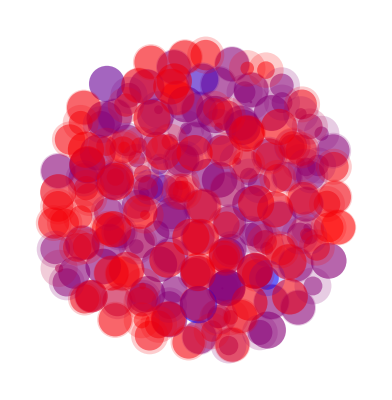

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin),0,1-( GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin),0,1-( GAbsRate[[maxstep,slice[[k]]]]-GAbsRatemin)/(GAbsRatemax-GAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Consumo di glucosio

Max GConsRate 0.00151601

Min GConsRate -0.0015147

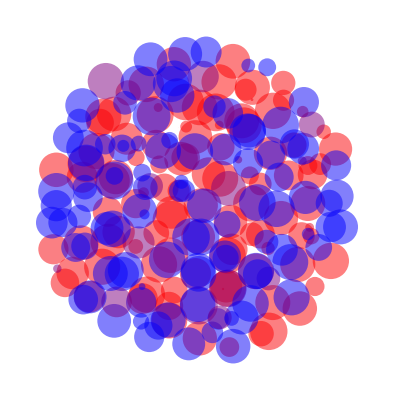

```mathematica
GConsRatemax =Max[GConsRate[[maxstep,slice]]]; 
GConsRatemin =Min[GConsRate[[maxstep,slice]]]; 

Print["Max GConsRate ",GConsRatemax];
Print["Min GConsRate ",GConsRatemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin),0,1-( GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

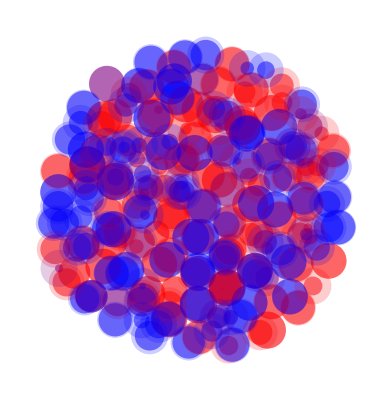

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin),0,1-( GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin),0,1-( GConsRate[[maxstep,slice[[k]]]]-GConsRatemin)/(GConsRatemax-GConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Concentrazione della glutammina extracellulare

Max Aextra concentration 5.49569

Min Aextra concentration 0.000399751

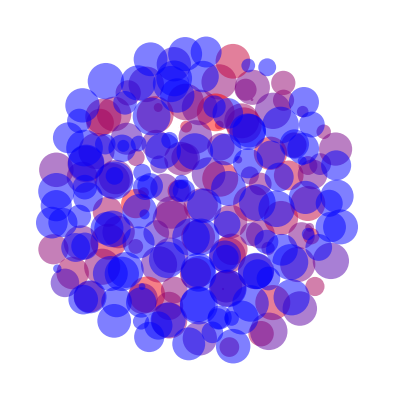

```mathematica
Amax =Max[Aextra[[maxstep,slice]]]; 
Amin=Min[Aextra[[maxstep,slice]]]; 

Print["Max Aextra concentration ",Amax];
Print["Min Aextra concentration ",Amin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin),0,1-( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

#### con effetto di sfuocatura

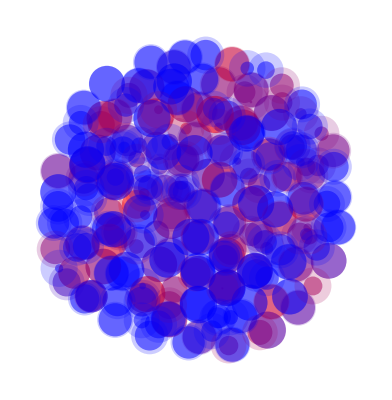

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin),0,1-( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],
Graphics[{Opacity[0.2],Table[{RGBColor[ ( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin),0,1-( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Assorbimento di glutammina

Max AAbsRate 0.00039992

Min AAbsRate -0.0000314775

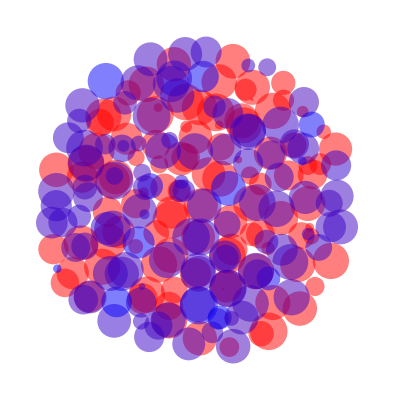

```mathematica
AAbsRatemax =Max[AAbsRate[[maxstep,slice]]]; 
AAbsRatemin =Min[AAbsRate[[maxstep,slice]]]; 

Print["Max AAbsRate ",AAbsRatemax];
Print["Min AAbsRate ",AAbsRatemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin),0,1-( AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

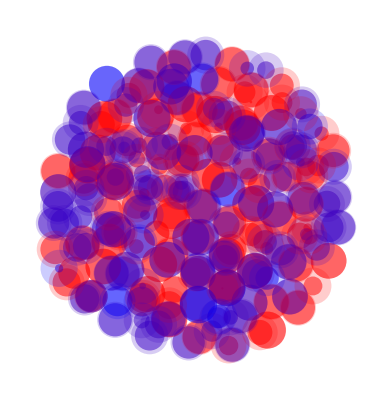

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin),0,1-( AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin),0,1-( AAbsRate[[maxstep,slice[[k]]]]-AAbsRatemin)/(AAbsRatemax-AAbsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Consumo di glutammina

Max AConsRate 0.0000852784

Min AConsRate -0.0000975007

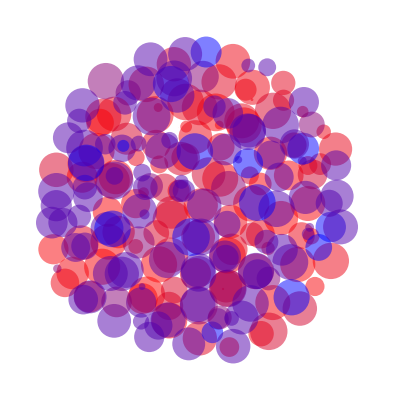

```mathematica
AConsRatemax =Max[AConsRate[[maxstep,slice]]]; 
AConsRatemin =Min[AConsRate[[maxstep,slice]]]; 

Print["Max AConsRate ",AConsRatemax];
Print["Min AConsRate ",AConsRatemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin),0,1-( AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

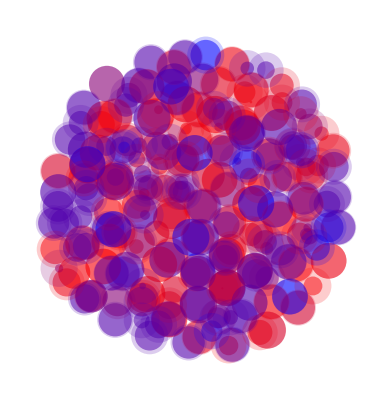

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin),0,1-( AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin),0,1-( AConsRate[[maxstep,slice[[k]]]]-AConsRatemin)/(AConsRatemax-AConsRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Concentrazione del'AcL extracellulare

Max AcLextra concentration 0.087947

Min AcLextra concentration 2.63757×10^-6

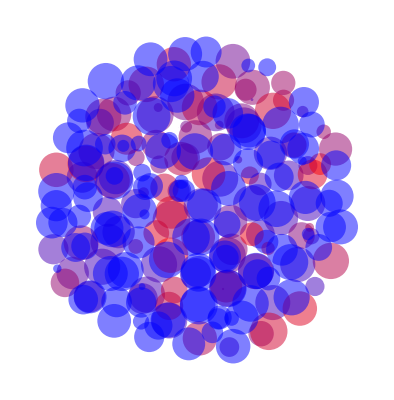

```mathematica
AcLmax =Max[AcLextra[[maxstep,slice]]]; 
AcLmin=Min[AcLextra[[maxstep,slice]]]; 

Print["Max AcLextra concentration ",AcLmax];
Print["Min AcLextra concentration ",AcLmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin),0,1-( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

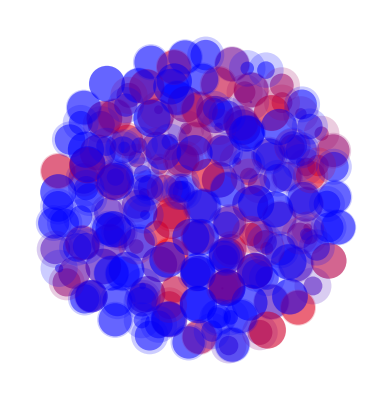

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ ( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin),0,1-( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ ( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin),0,1-( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### pH extracellulare

Max pH 401.448

Min pH 7.35113

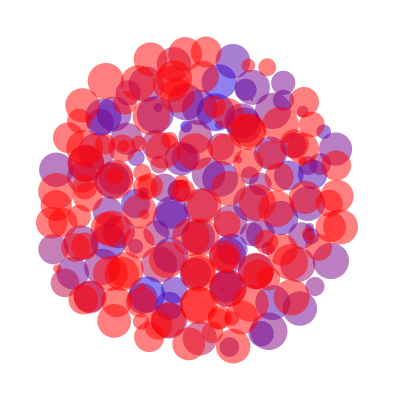

```mathematica
pHmax =Max[pH[[maxstep,slice]]]; 
pHmin =Min[pH[[maxstep,slice]]]; 

Print["Max pH ",pHmax];
Print["Min pH ",pHmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[  1-(pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin),0,( pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

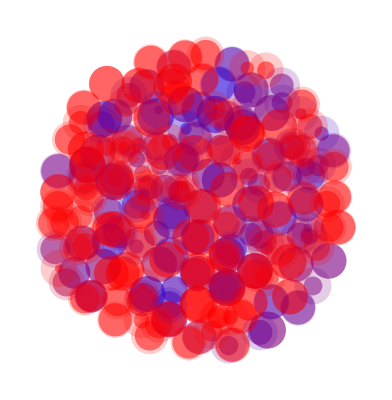

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[  1-(pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin),0,( pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[  1-(pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin),0,( pH[[maxstep,slice[[k]]]]-pHmin)/(pHmax-pHmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### ATPp

Max ATPp 18.2279

Min ATPp 2.38155×10^-6

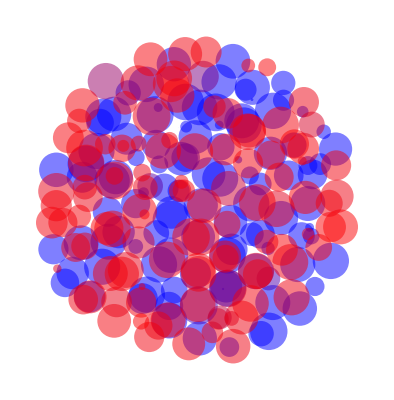

```mathematica
ATPpmax =Max[ATPp[[maxstep,slice]]]; 
ATPpmin =Min[ATPp[[maxstep,slice]]]; 

Print["Max ATPp ",ATPpmax];
Print["Min ATPp ",ATPpmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin),0,1-( ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

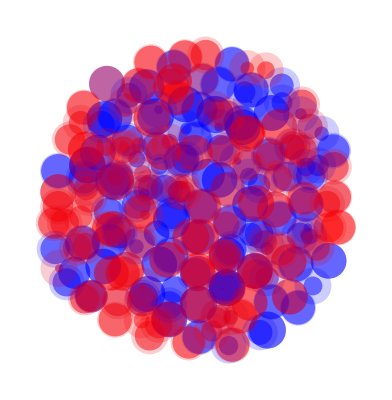

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin),0,1-( ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin),0,1-( ATPp[[maxstep,slice[[k]]]]-ATPpmin)/(ATPpmax-ATPpmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Store

Max Store 3.80812

Min Store 6.23453×10^-6

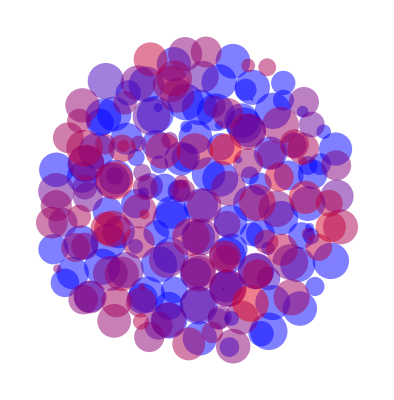

```mathematica
Storemax =Max[Store[[maxstep,slice]]]; 
Storemin =Min[Store[[maxstep,slice]]]; 

Print["Max Store ",Storemax];
Print["Min Store ",Storemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin),0,1-( Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

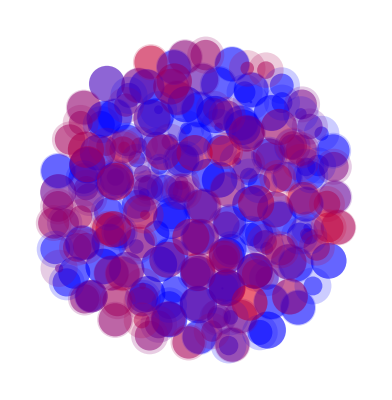

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin),0,1-( Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin),0,1-( Store[[maxstep,slice[[k]]]]-Storemin)/(Storemax-Storemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### protein

Max protein 65.7091

Min protein 7.35168

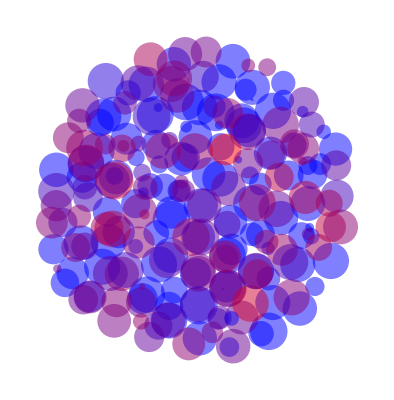

```mathematica
proteinmax =Max[protein[[maxstep,slice]]]; 
proteinmin =Min[protein[[maxstep,slice]]]; 

Print["Max protein ",proteinmax];
Print["Min protein ",proteinmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin),0,1-( protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

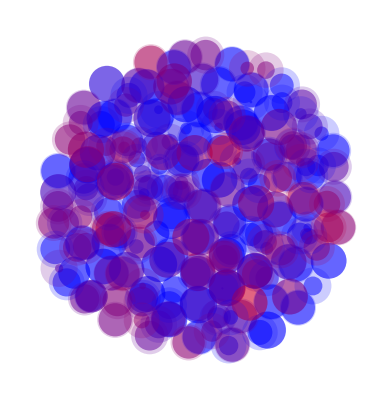

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin),0,1-( protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin),0,1-( protein[[maxstep,slice[[k]]]]-proteinmin)/(proteinmax-proteinmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### rate di produzione di proteine

Max protRate 58.4605

Min protRate 0.000299675

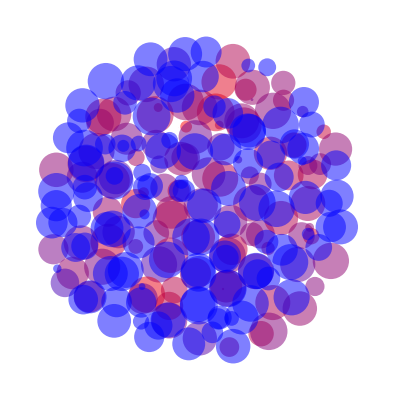

```mathematica
protRatemax =Max[protRate[[maxstep,slice]]]; 
protRatemin =Min[protRate[[maxstep,slice]]]; 

Print["Max protRate ",protRatemax];
Print["Min protRate ",protRatemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin),0,1-( protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

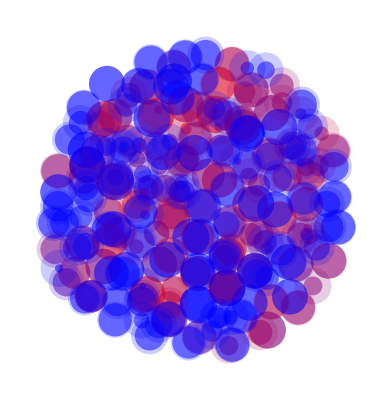

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin),0,1-( protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin),0,1-( protRate[[maxstep,slice[[k]]]]-protRatemin)/(protRatemax-protRatemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### rate di produzione di DNA

Max DNArate 0.001

Min DNArate 0.

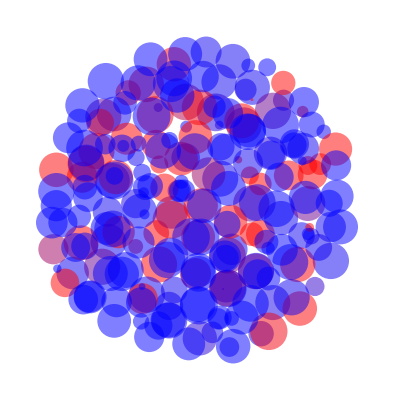

```mathematica
DNAratemax =Max[DNArate[[maxstep,slice]]]; 
DNAratemin =Min[DNArate[[maxstep,slice]]]; 

Print["Max DNArate ",DNAratemax];
Print["Min DNArate ",DNAratemin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin),0,1-( DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

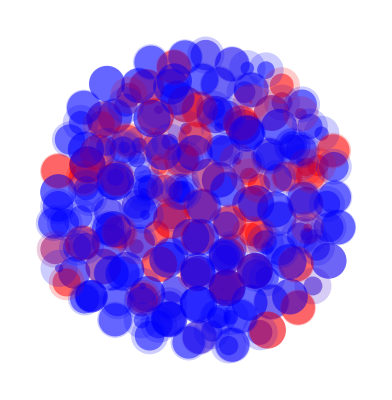

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin),0,1-( DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin),0,1-( DNArate[[maxstep,slice[[k]]]]-DNAratemin)/(DNAratemax-DNAratemin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Mitocondri

Max Mit 447.895

Min Mit 13.6969

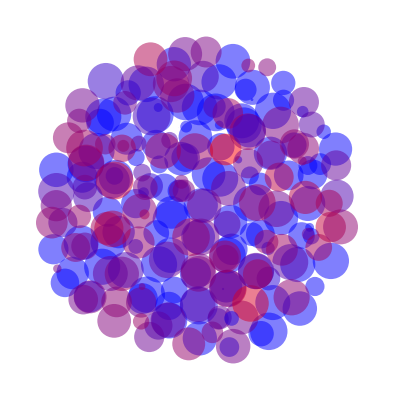

```mathematica
Mitmax =Max[Mit[[maxstep,slice]]]; 
Mitmin =Min[Mit[[maxstep,slice]]]; 

Print["Max Mit ",Mitmax];
Print["Min Mit ",Mitmin];

Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin),0,1-( Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],PlotRange->All]];
```

#### con effetto di sfuocatura

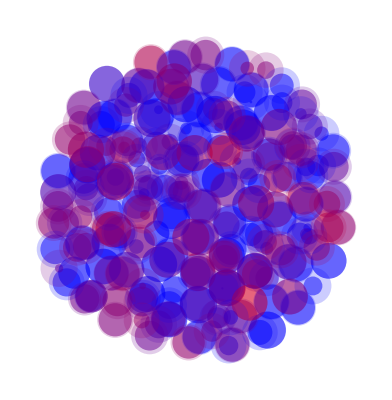

```mathematica
Print[Show[Graphics[{Opacity[0.5],Table[{RGBColor[ (Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin),0,1-( Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}]}],Graphics[{Opacity[0.2],Table[{RGBColor[ (Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin),0,1-( Mit[[maxstep,slice[[k]]]]-Mitmin)/(Mitmax-Mitmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]]]},{k,1,Length[slice]}]}],
PlotRange->All]];
```

### Visualizzazione del flusso di O2 (sovrapposto a concentrazione)

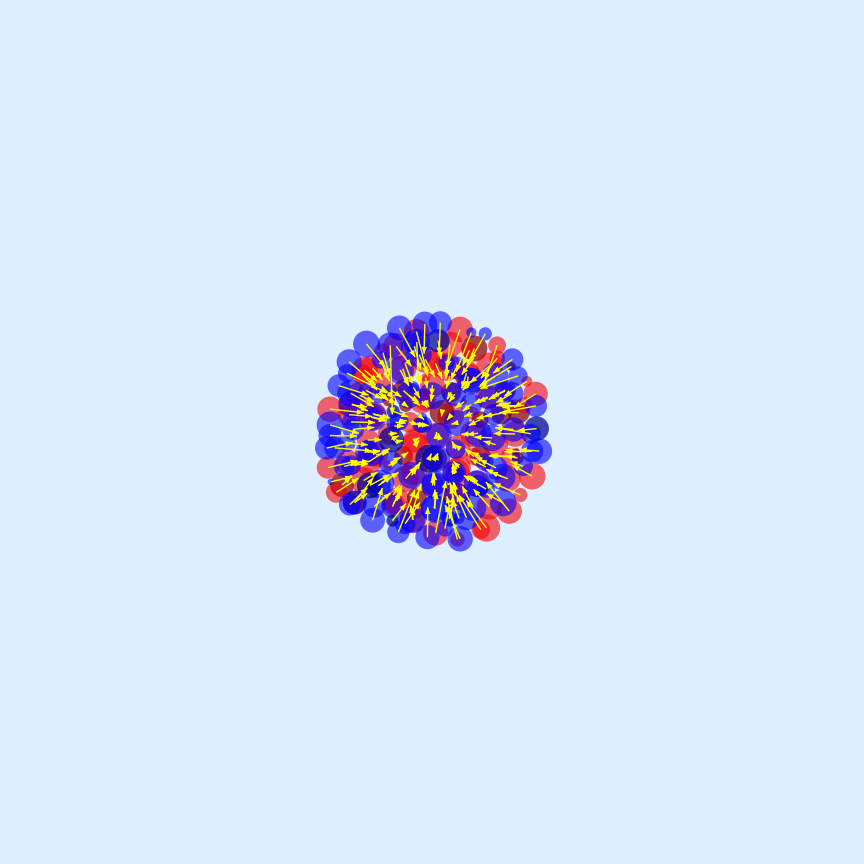

```mathematica
O2max =Max[O2[[maxstep,slice]]]; 
O2min =Min[O2[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fO2max=Max[Map[Norm,fO2slice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min),0,1-( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fO2slice[[k,{1,2}]]/fO2max}],{k,1,Length[slice]}]}],PlotRange->{{-200,200},{-200,200}},ImageSize->12*72,Background->LightBlue]];
```

#### con effetto di sfuocatura

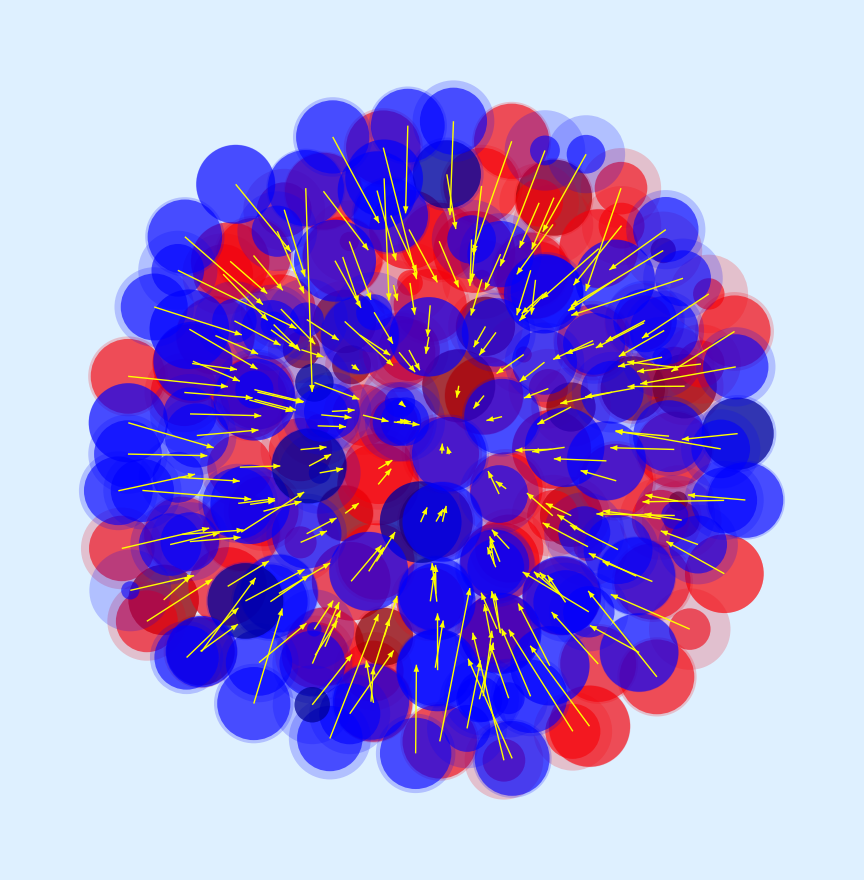

```mathematica
O2max =Max[O2[[maxstep,slice]]]; 
O2min =Min[O2[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fO2max=Max[Map[Norm,fO2slice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min),0,1-( O2[[maxstep,slice[[k]]]]-O2min)/(O2max-O2min)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Opacity[0.2],
Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fO2slice[[k,{1,2}]]/fO2max}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### Visualizzazione senzs display della concentrazione

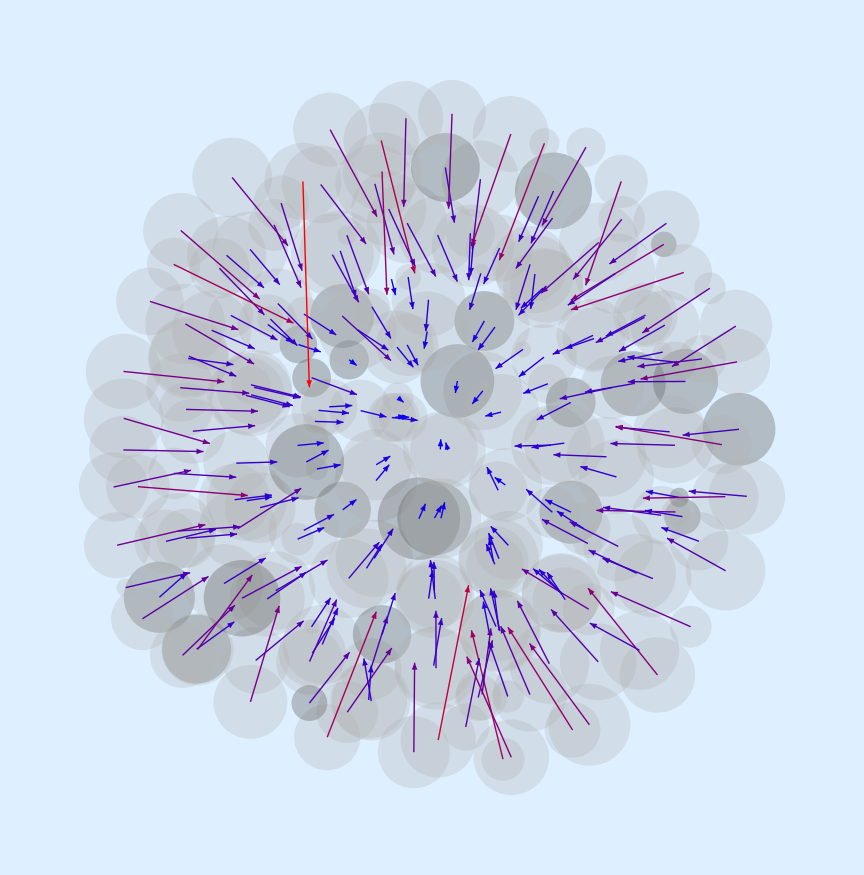

```mathematica
Print[Show[Graphics[{Table[{Opacity[0.3],GrayLevel[0.7],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ], Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.15],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Arrowheads[Small],Table[{RGBColor[Norm[fO2slice[[k]] ]/fO2max,0,1-Norm[fO2slice[[k ]] ]/fO2max],
Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fO2slice[[k,{1,2}]]/fO2max}]},{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

### Visualizzazione del flusso di G extracellulare (sovrapposto a concentrazione)

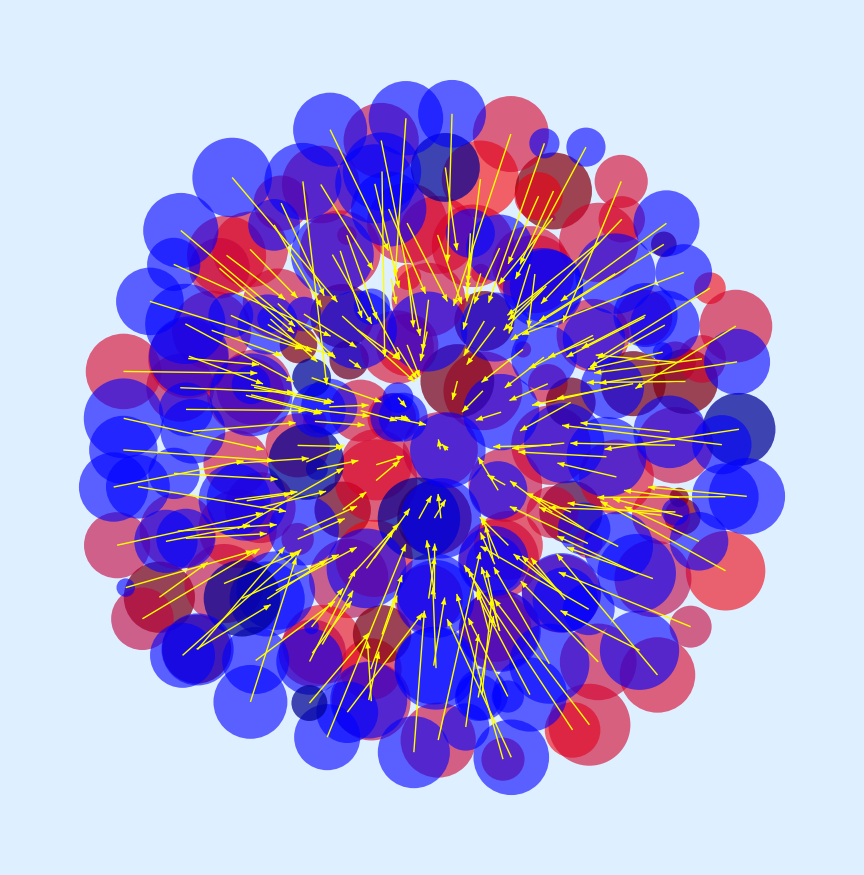

```mathematica
Gmax =Max[Gextra[[maxstep,slice]]]; 
Gmin =Min[Gextra[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fGmax=Max[Map[Norm,fGslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin),0,1-( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fGslice[[k,{1,2}]]/fGmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### con effetto di sfuocatura

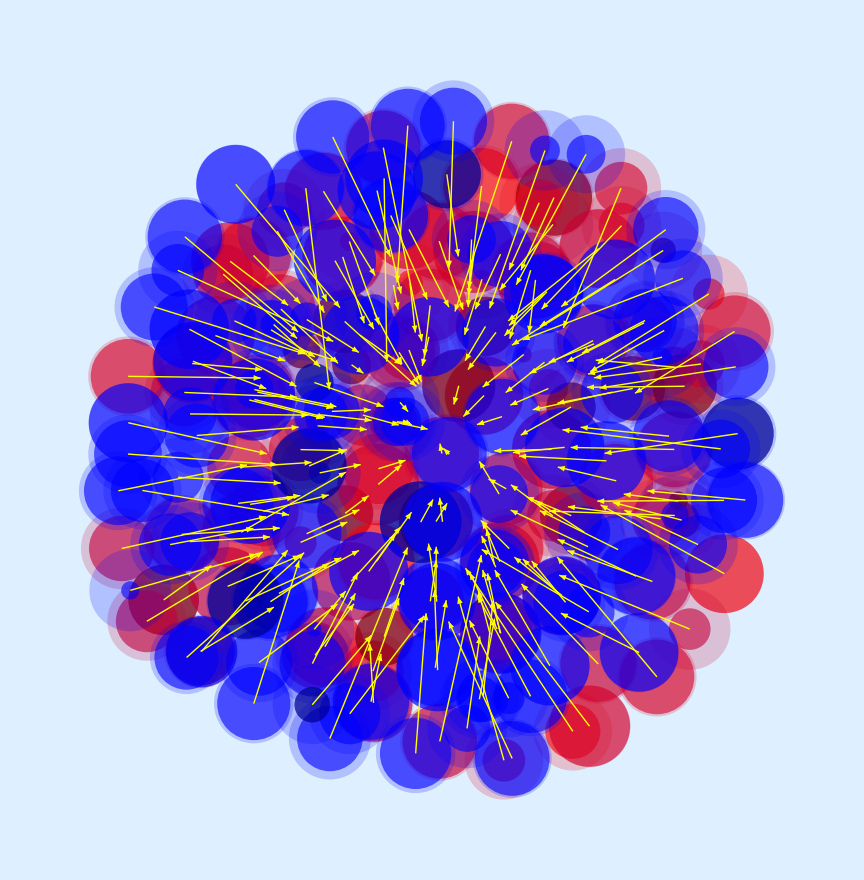

```mathematica
Gmax =Max[Gextra[[maxstep,slice]]]; 
Gmin =Min[Gextra[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fGmax=Max[Map[Norm,fGslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin),0,1-( Gextra[[maxstep,slice[[k]]]]-Gmin)/(Gmax-Gmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Opacity[0.2],
Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fGslice[[k,{1,2}]]/fGmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### Visualizzazione senzs display della concentrazione

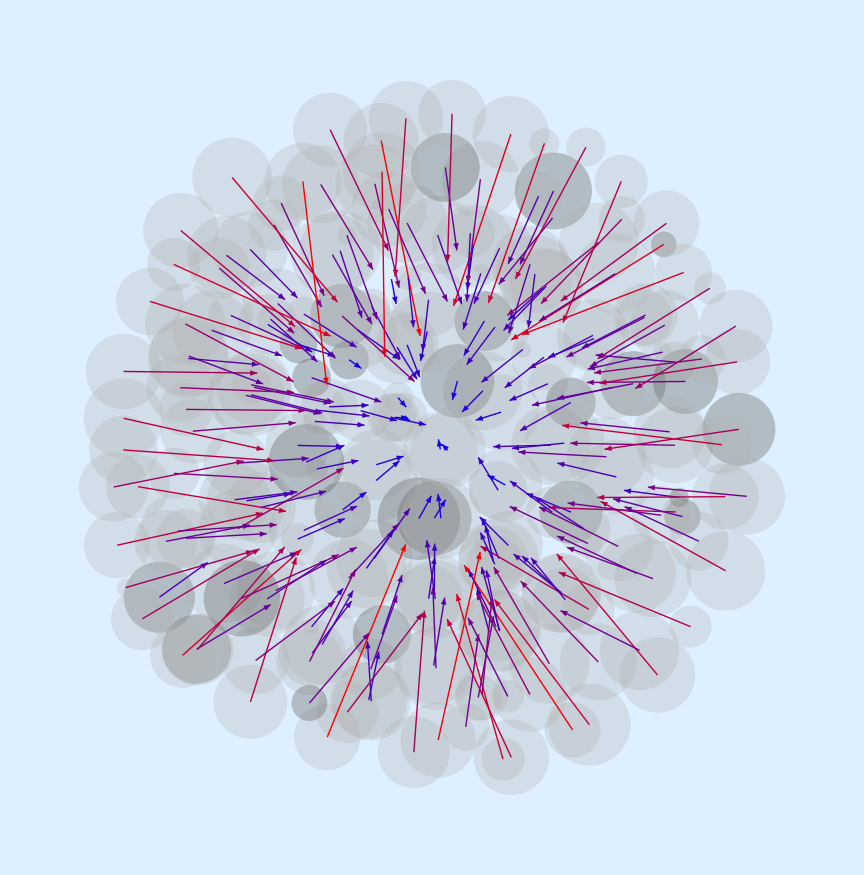

```mathematica
Print[Show[Graphics[{Table[{Opacity[0.3],GrayLevel[0.7],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ], Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.15],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Arrowheads[Small],Table[{RGBColor[Norm[fGslice[[k]]]/fGmax,0,1-Norm[fGslice[[k]]]/fGmax],
Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fGslice[[k,{1,2}]]/fGmax}]},{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

### Visualizzazione del flusso di glutammina extracellulare (sovrapposto a concentrazione)

Aextra (max): 5.49569

Aextra (min): 0.000399751

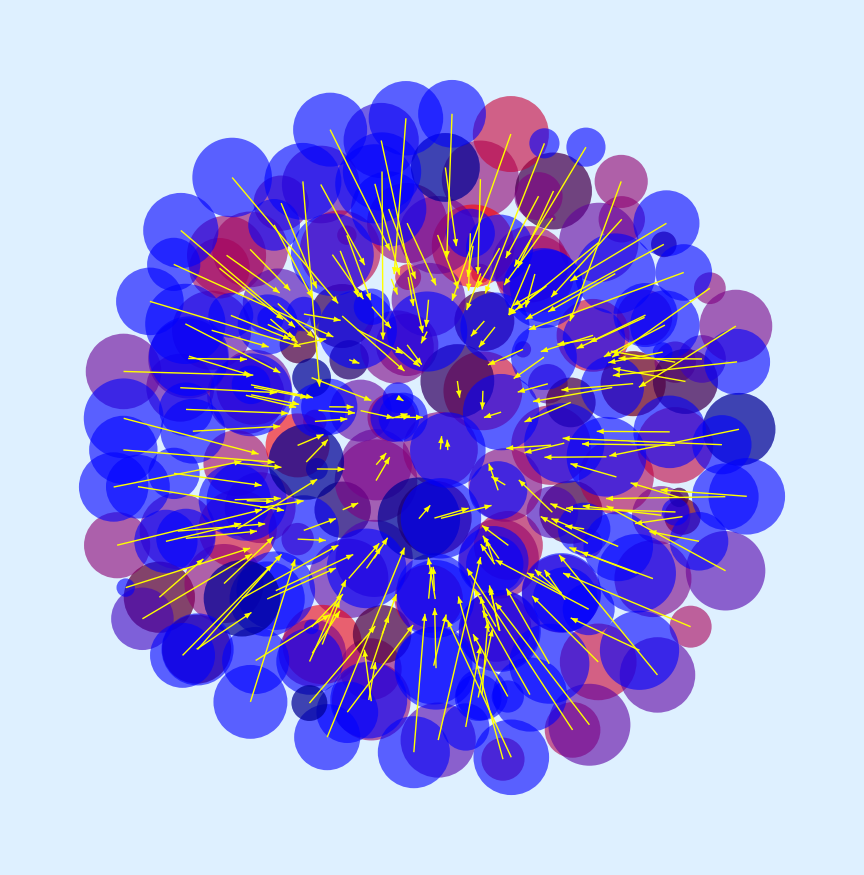

```mathematica
Amax =Max[Aextra[[maxstep,slice]]]; 
Amin =Min[Aextra[[maxstep,slice]]]; 

Print["Aextra (max): ",Amax];
Print["Aextra (min): ",Amin];

rmax  =Max[Map[Norm,r[[maxstep]]]];

fAmax=Max[Map[Norm,fAslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin),0,1-( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fAslice[[k,{1,2}]]/fAmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### con effetto di sfuocatura

Aextra (max): 5.49569

Aextra (min): 0.000399751

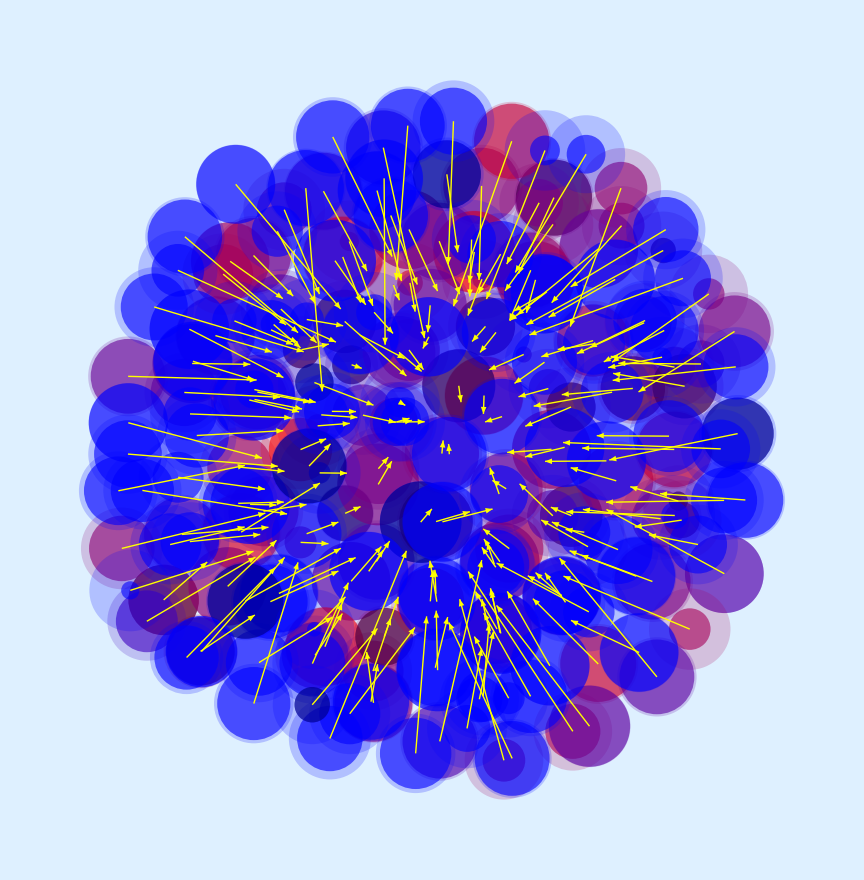

```mathematica
Amax =Max[Aextra[[maxstep,slice]]]; 
Amin =Min[Aextra[[maxstep,slice]]]; 

Print["Aextra (max): ",Amax];
Print["Aextra (min): ",Amin];

rmax  =Max[Map[Norm,r[[maxstep]]]];

fAmax=Max[Map[Norm,fAslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin),0,1-( Aextra[[maxstep,slice[[k]]]]-Amin)/(Amax-Amin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Opacity[0.2],
Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fAslice[[k,{1,2}]]/fAmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### Visualizzazione senzs display della concentrazione

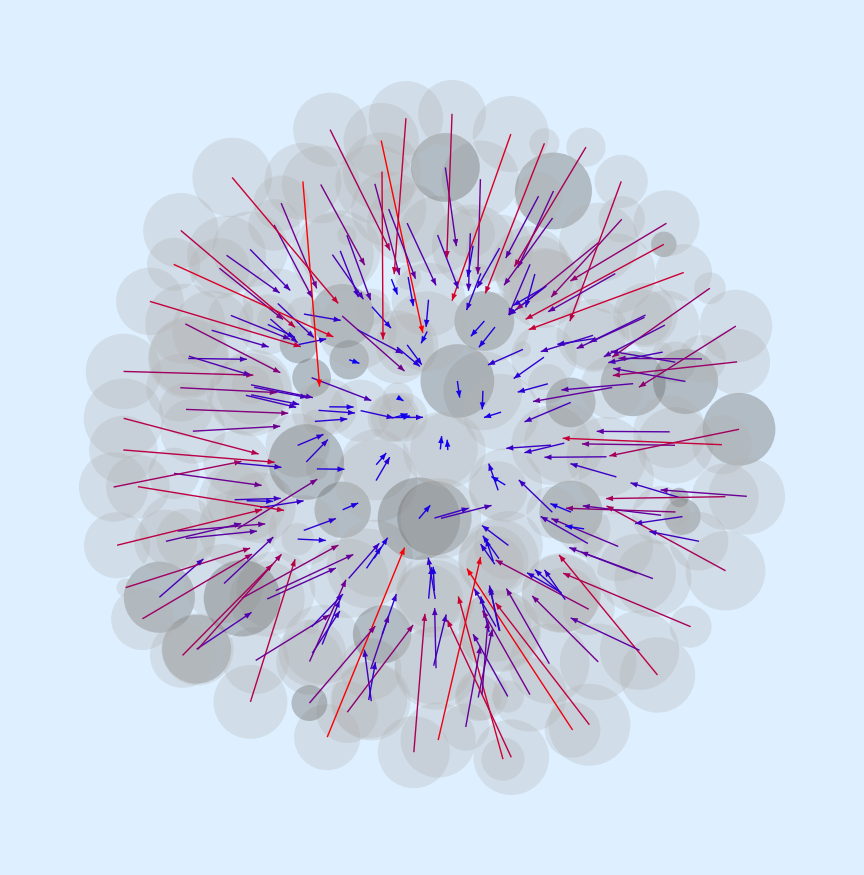

```mathematica
Print[Show[Graphics[{Table[{Opacity[0.3],GrayLevel[0.7],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ], Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.15],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Arrowheads[Small],Table[{RGBColor[Norm[fAslice[[k]] ]/fAmax,0,1-Norm[fAslice[[k]]  ]/fAmax],
Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fAslice[[k,{1,2}]]/fAmax}]},{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

### Visualizzazione del flusso di AcL extracellulare (sovrapposto a concentrazione)

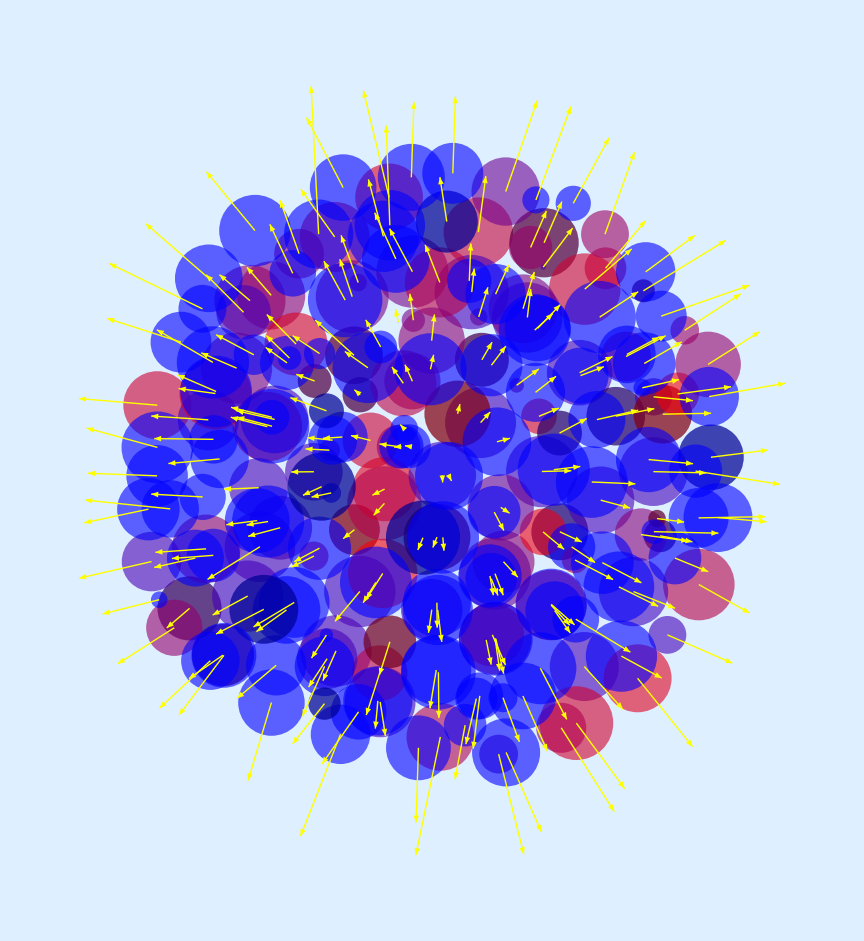

```mathematica
AcLmax =Max[AcLextra[[maxstep,slice]]]; 
AcLmin =Min[AcLextra[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fAcLmax=Max[Map[Norm,fAcLslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin),0,1-( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+4*rmax*fAcLslice[[k,{1,2}]]/fAcLmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### con effetto di sfuocatura

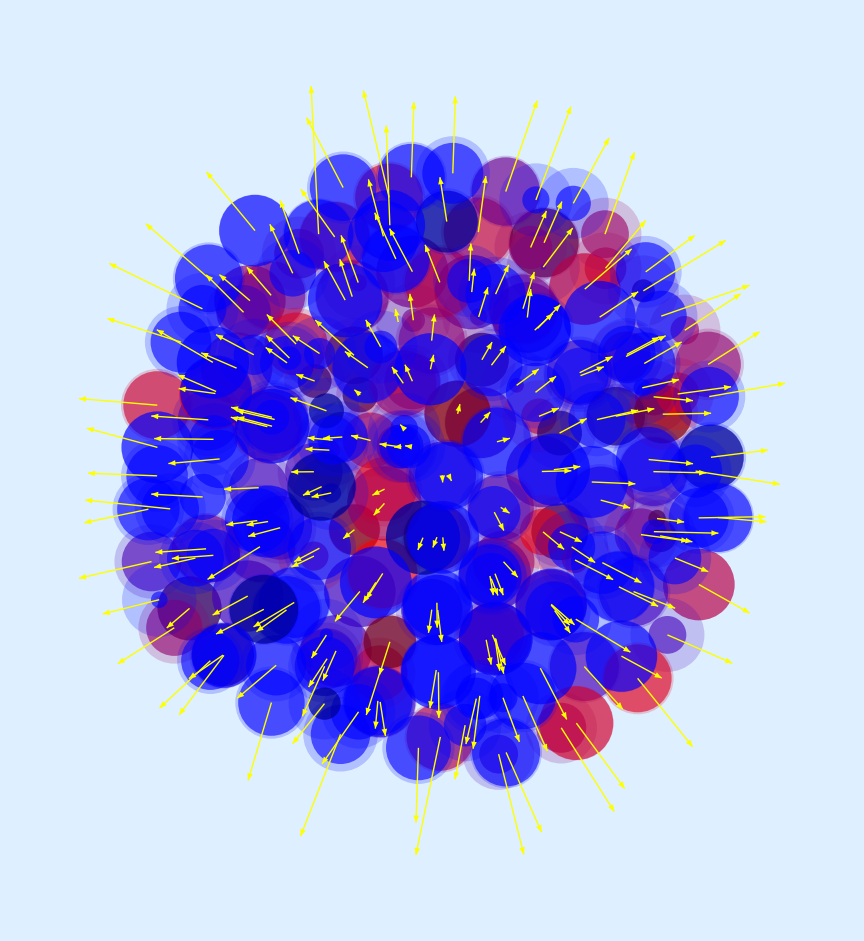

```mathematica
AcLmax =Max[AcLextra[[maxstep,slice]]]; 
AcLmin =Min[AcLextra[[maxstep,slice]]]; 

rmax  =Max[Map[Norm,r[[maxstep]]]];

fAcLmax=Max[Map[Norm,fAcLslice]];

Print[Show[Graphics[{AbsoluteThickness[1],Table[{Opacity[0.6],RGBColor[ ( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin),0,1-( AcLextra[[maxstep,slice[[k]]]]-AcLmin)/(AcLmax-AcLmin)],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ],
Opacity[0.2],
Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},r[[maxstep,slice[[k]]]] ],
Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.3],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Yellow,Arrowheads[Small],AbsoluteThickness[1],Table[Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+4*rmax*fAcLslice[[k,{1,2}]]/fAcLmax}],{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

#### Visualizzazione senzs display della concentrazione

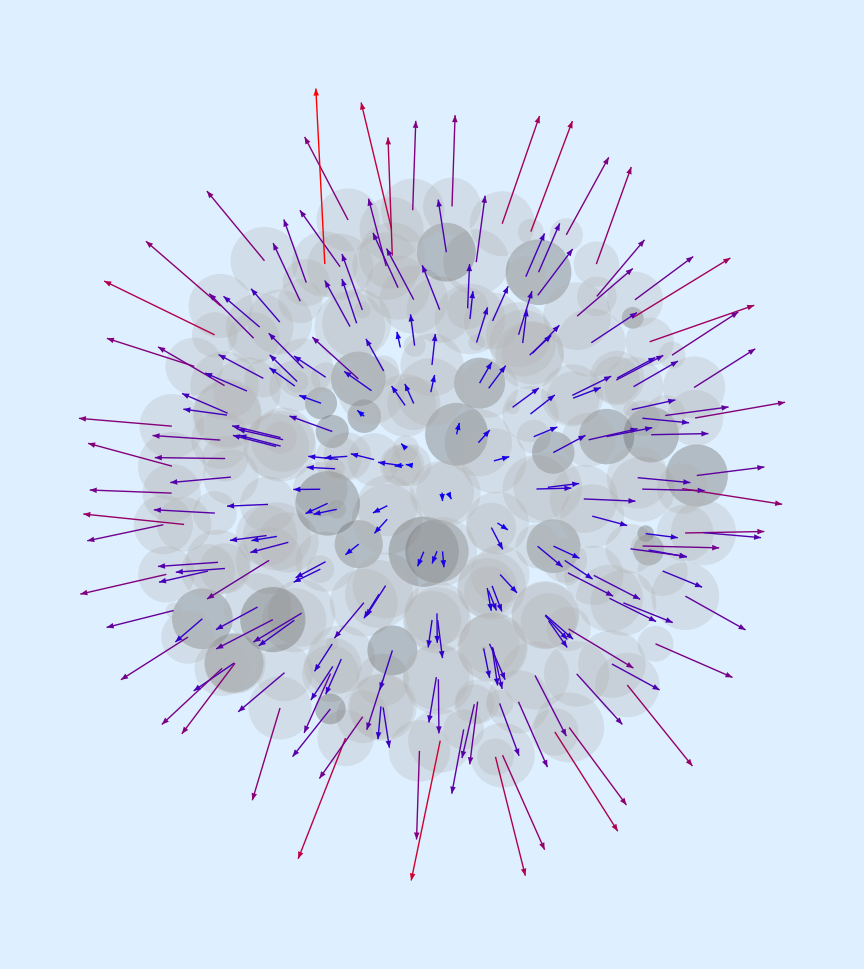

```mathematica
Print[Show[Graphics[{Table[{Opacity[0.3],GrayLevel[0.7],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ], Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.15],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Arrowheads[Small],Table[{RGBColor[Norm[fAcLslice[[k]] ]/fAcLmax,0,1-Norm[fAcLslice[[k]] ]/fAcLmax],
Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*fAcLslice[[k,{1,2}]]/fAcLmax}]},{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

### Velocità

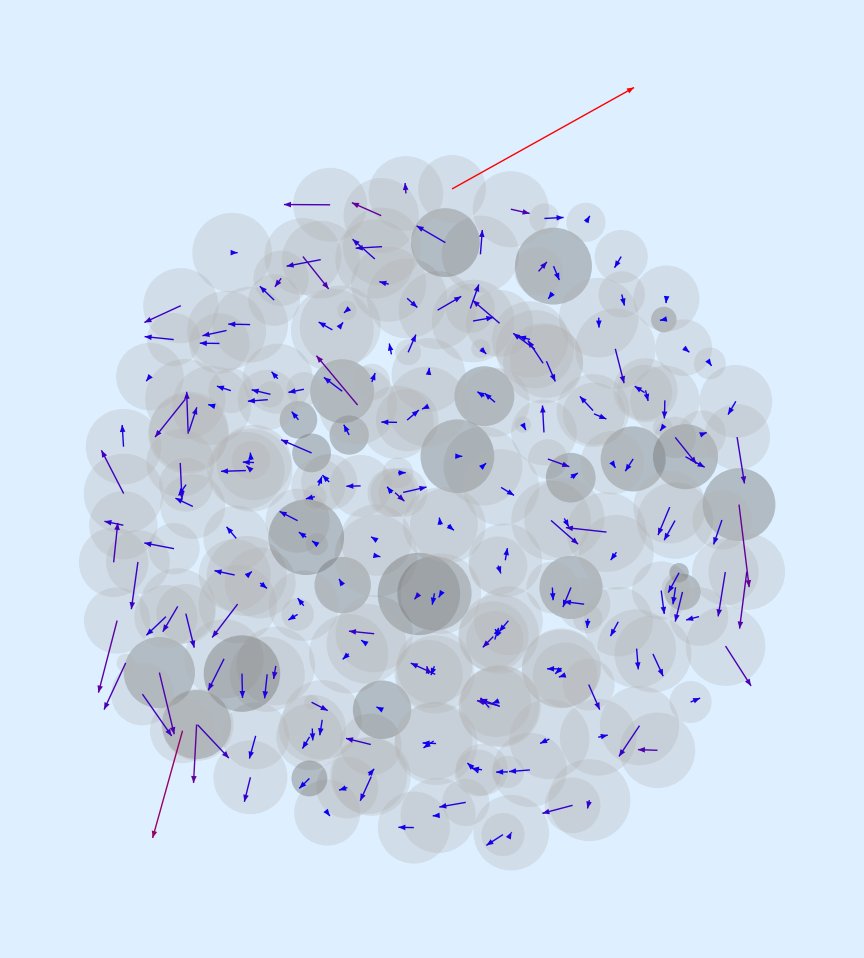

```mathematica
vmax=Max[Map[Norm,Transpose[Transpose[vslice][[{1,2}]]]]];

Print[Show[Graphics[{Table[{Opacity[0.3],GrayLevel[0.7],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ], Black,If[phase[[maxstep,slice[[k]]]] == 6,Opacity[0.15],Opacity[0]],Disk[{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},Sqrt[r[[maxstep,slice[[k]]]]^2-(zpos[[slice[[k]]]]-zheight)^2] ]},{k,1,Length[slice]}],
Opacity[1],Arrowheads[Small],Table[{RGBColor[Norm[v[[maxstep,slice[[k]]]] ]/vmax,0,1-Norm[v[[maxstep,slice[[k]] ]] ]/vmax],
Arrow[{{xpos[[slice[[k]]]],ypos[[slice[[k]]]]},{xpos[[slice[[k]]]],ypos[[slice[[k]]]]}+5*rmax*vslice[[k,{1,2}]]/vmax}]},{k,1,Length[slice]}]}],PlotRange->All,ImageSize->12*72,Background->LightBlue]];
```

## Plots

#### Costruzione della lista indicizzata ordinata delle cellule (ordine di distanza dal centro)

```mathematica
r0 = Map[Norm,Table[x[[maxstep,k]]-ct[[maxstep]],{k,1,ncells[[maxstep]]}]];
```

```mathematica
rstep = 10; (* passo di 10 micron *)
nshellmax=Ceiling[Max[r0]/rstep];
Print["Disk has ",nshellmax," shells"];
shell=Ceiling[r0/rstep];
nshell=Table[0,{nshellmax}];
nliveshell=Table[0,{nshellmax}];
cell=Table[{},{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
nshell[[shell[[k]]]]++;
If[phase[[maxstep,k]]≠6,nliveshell[[shell[[k]]]]++];
AppendTo[cell[[shell[[k]]]],k];
k++];
Print[nshell]
```

Disk has 7 shells

{4,33,91,178,287,383,194}

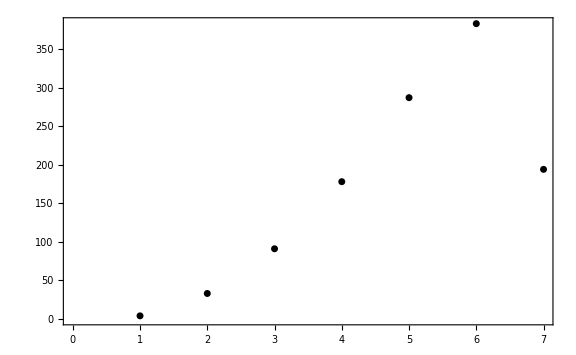

```mathematica
ListPlot[nshell,Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

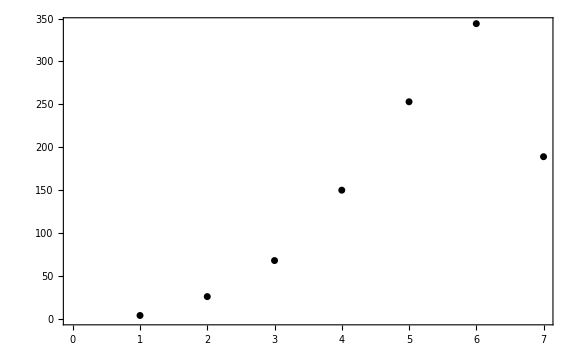

```mathematica
ListPlot[nliveshell,Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

```mathematica
Apply[Plus,nshell]
```

1170

```mathematica
rshell=Table[0.5*rstep*(2*k-1),{k,1,nshellmax}]
```

{5.,15.,25.,35.,45.,55.,65.}

### Dimensioni cellulari (raggio, µm) vs. distanza da centroide (µm)

```mathematica
rShell=r2Shell = Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
rShell[[shell[[k]]]]+= r[[maxstep,k]];
r2Shell[[shell[[k]]]]+= r[[maxstep,k]]^2;
k++];
rSa=Table[If[nshell[[k]]>0,rShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
rSa2=Table[If[nshell[[k]]>0,r2Shell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
sigma =Table[If[nshell[[k]]>0,Sqrt[rSa2[[k]]-rSa[[k]]^2]/Sqrt[nshell[[k]]],0],{k,1,nshellmax}];
rmin= Min[r[[maxstep]]];
rmax= Max[r[[maxstep]]];
```

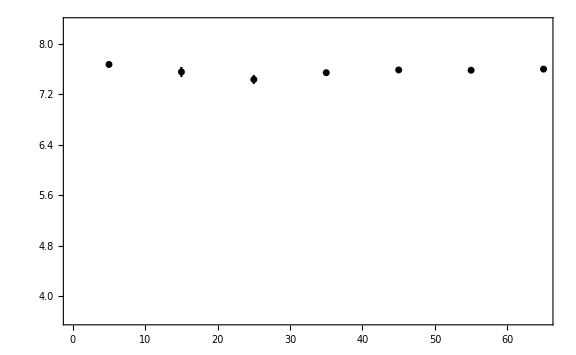

```mathematica
plrSa=ErrorListPlot[Transpose[{rshell,rSa,sigma}],PlotRange->{rmin-0.1(rmax-rmin),rmax+0.1(rmax-rmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Età cellulare (età, s, solo cellule vive) vs. distanza da centroide (µm)

```mathematica
ageinShell=agein2Shell =agemininShell=agemaxinShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]≠6,
ageinShell[[shell[[k]]]]+= age[[maxstep,k]];
agein2Shell[[shell[[k]]]]+= age[[maxstep,k]]^2];
k++];
For[k=1,k≤nshellmax,
If[phase[[maxstep,k]]≠6,
agemininShell[[k]]=Min[age[[maxstep,cell[[k]]]] ];
agemaxinShell[[k]]=Max[age[[maxstep,cell[[k]]]] ]];
k++];
ageSa=Table[If[nliveshell[[k]]>0,ageinShell[[k]]/nliveshell[[k]],0],{k,1,nshellmax}];
ageSa2=Table[If[nliveshell[[k]]>0,agein2Shell[[k]]/nliveshell[[k]],0],{k,1,nshellmax}];
sigma =Table[If[nliveshell[[k]]>0,Sqrt[ageSa2[[k]]-ageSa[[k]]^2]/Sqrt[nliveshell[[k]]],0],{k,1,nshellmax}];
agemin= Min[age[[maxstep]]];
agemax= Max[age[[maxstep]]];
```

```mathematica
plageSa=Show[ErrorListPlot[Transpose[{rshell,ageSa,sigma}],PlotRange->{0,1.1*Max[ageSa]},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]],ListPlot[Transpose[{rshell,agemaxinShell}],PlotRange->{agemin,agemax},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Red,AbsolutePointSize[3]]],ListPlot[Transpose[{rshell,agemininShell}],PlotRange->{agemin,agemax},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Red,AbsolutePointSize[3]]]]
```

-Graphics-

### Conc.glucosio interno al tempo massimo (kg/m^3) vs. distanza da centroide (µm)

```mathematica
mGinShell=mGin2Shell=concGin=concGin2=sigma=Table[0,{nshellmax}];

For[k=1,k≤ncells[[maxstep]],
mGinShell[[shell[[k]]]]+=10^18 * G[[maxstep,k]]/volume[[k]];
mGin2Shell[[shell[[k]]]]+=(10^18 * G[[maxstep,k]]/volume[[k]])^2;
k++];

For[k=1,k≤nshellmax,
If[nshell[[k]]>0,
concGin[[k]]=(mGinShell[[k]])/nshell[[k]];
concGin2[[k]]=(mGin2Shell[[k]])/nshell[[k]];
sigma[[k]] = Sqrt[concGin2[[k]]-concGin[[k]]^2]/Sqrt[nshell[[k]]],
0];
k++];

minconcGin=Min[concGin];
maxconcGin=Max[concGin];
```

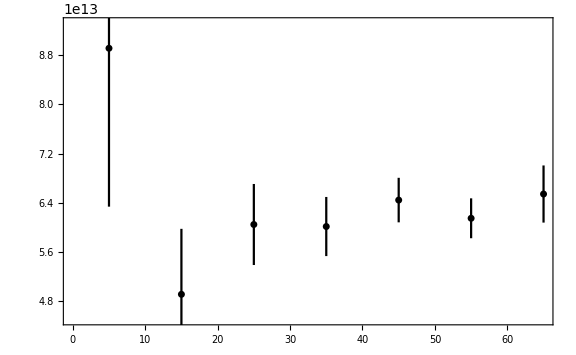

```mathematica
plGin=ErrorListPlot[Transpose[{rshell,concGin,sigma}],PlotRange->{minconcGin-0.1*(maxconcGin-minconcGin),maxconcGin+0.1*(maxconcGin-minconcGin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Conc.glucosio extracell al tempo massimo (kg/m^3) vs. distanza da centroide (µm)

```mathematica
GextraShell=GextraShell2=concGextra=concGextra2=sigma=Table[0,{nshellmax}];

For[k=1,k≤ncells[[maxstep]],
GextraShell[[shell[[k]]]]+= Gextra[[maxstep,k]];
GextraShell2[[shell[[k]]]]+= Gextra[[maxstep,k]]^2;
k++];

For[k=1,k≤nshellmax,
If[nshell[[k]]>0,
concGextra[[k]]=(GextraShell[[k]])/nshell[[k]];
concGextra2[[k]]=(GextraShell2[[k]])/nshell[[k]];
sigma[[k]] = Sqrt[concGextra2[[k]]-concGextra[[k]]^2]/Sqrt[nshell[[k]]],
0];
k++];

minconcGextra=Min[concGextra];
maxconcGextra=Max[concGextra];
```

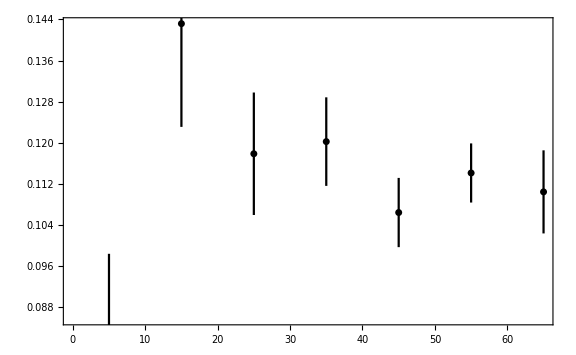

```mathematica
plGextra=ErrorListPlot[Transpose[{rshell,concGextra,sigma}],(*PlotRange->{minconcGextra-0.1*(maxconcGextra-minconcGextra),maxconcGextra+0.1*(maxconcGextra-minconcGextra)},*)Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### pH vs. distanza da centroide (µm)

```mathematica
pHinShell=pHinShell2=pHaverage=pHaverage2=pHaveragesigma=Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
pHinShell[[shell[[k]]]]+=pH[[maxstep,k]];
pHinShell2[[shell[[k]]]]+=pH[[maxstep,k]]^2;
k++];

For[k=1,k≤nshellmax,
If[nshell[[k]]>0,
pHaverage[[k]]=(pHinShell[[k]])/nshell[[k]];
pHaverage2[[k]]=(pHinShell2[[k]])/nshell[[k]];
pHaveragesigma[[k]] = Sqrt[pHaverage2[[k]]-pHaverage[[k]]^2]/nshell[[k]],
0];
k++];

minpHaverage=Min[pHaverage];
maxpHaverage=Max[pHaverage];
```

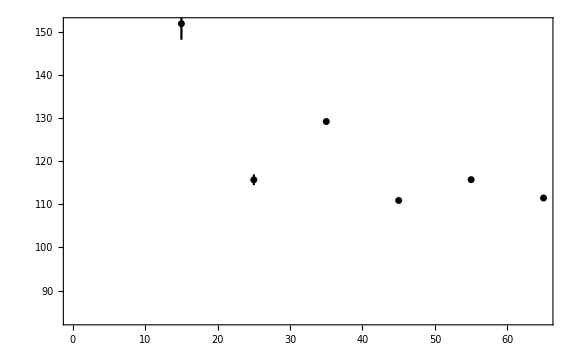

```mathematica
plpH=ErrorListPlot[Transpose[{rshell,pHaverage,pHaveragesigma}],(* PlotRange->All,*)Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### O2 vs. distanza da centroide (µm)

```mathematica
O2inShell=O2inShell2=Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
O2inShell[[shell[[k]]]]+=O2[[maxstep,k]];
O2inShell2[[shell[[k]]]]+=O2[[maxstep,k]]^2;
k++];
concO2in=Table[If[nshell[[k]]>0,(O2inShell[[k]])/nshell[[k]],0],{k,1,nshellmax}];
concO2in2=Table[If[nshell[[k]]>0,(O2inShell2[[k]])/nshell[[k]],0],{k,1,nshellmax}];
sigma = Table[If[nshell[[k]]>0,Sqrt[concO2in2[[k]]-concO2in[[k]]^2]/nshell[[k]],0],{k,1,nshellmax}];
minconcO2in=Min[concO2in];
maxconcO2in=Max[concO2in];
```

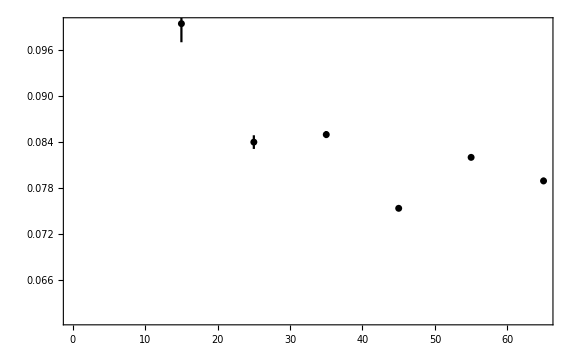

```mathematica
plO2=ErrorListPlot[Transpose[{rshell,concO2in,sigma}],(*PlotRange->All,*)Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

#### pressione parziale dell' O2 (in mmHg) in funzione della distanza dal centroide (in micron)

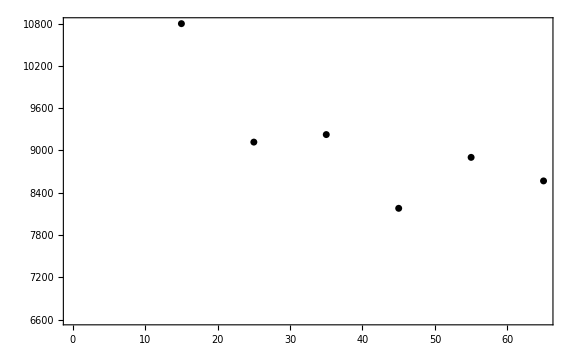

```mathematica
plO2=ListPlot[Transpose[{rshell,760*concO2in/.007}],(* PlotRange->All,*)Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

#### diminuzione della pressione parziale dell' O2 (in mmHg) in funzione della distanza dal centroide (in micron)

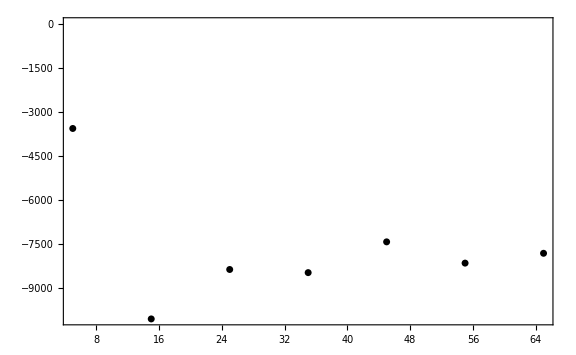

```mathematica
plO2=ListPlot[Transpose[{rshell,760-760*concO2in/.007}],PlotRange->All,Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

#### diminuzione della pressione parziale dell' O2 (in mbar) in funzione della distanza dal centroide (in micron)

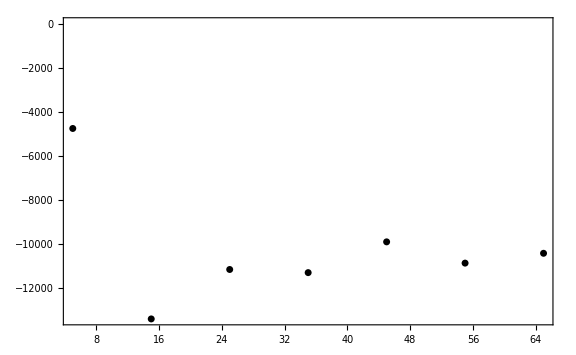

```mathematica
plO2=ListPlot[Transpose[{rshell,1013-1013*concO2in/.007}],PlotRange->All,Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Frazione di cellule morte (%) vs. distanza da centroide (µm)

```mathematica
deadinShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]==6,deadinShell[[shell[[k]]]]++ ];
k++];
deadfraction=100.*Table[If[nshell[[k]]>0,deadinShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
sigma = 100.*Table[If[nshell[[k]]>0 && deadinShell[[k]]>0,Sqrt[1/deadinShell[[k]]+ 1/nshell[[k]]]*(deadinShell[[k]]/nshell[[k]]),0],{k,1,nshellmax}];
```

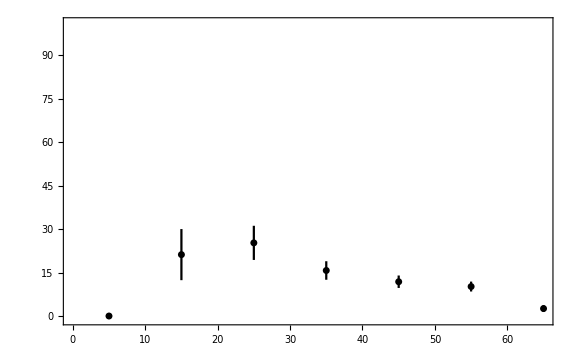

```mathematica
pldeadfraction=ErrorListPlot[Transpose[{rshell,deadfraction,sigma}],PlotRange->{-1,101},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Frazione di cellule vive (%) vs. distanza da centroide (µm)

```mathematica
liveinShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]!=6,liveinShell[[shell[[k]]]]++ ];
k++];
livefraction=100.*Table[If[nshell[[k]]>0,liveinShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
sigma = 100.*Table[If[nshell[[k]]>0 && liveinShell[[k]]>0,Sqrt[1/liveinShell[[k]]]+1/nshell[[k]]*(liveinShell[[k]]/nshell[[k]]),0],{k,1,nshellmax}];
```

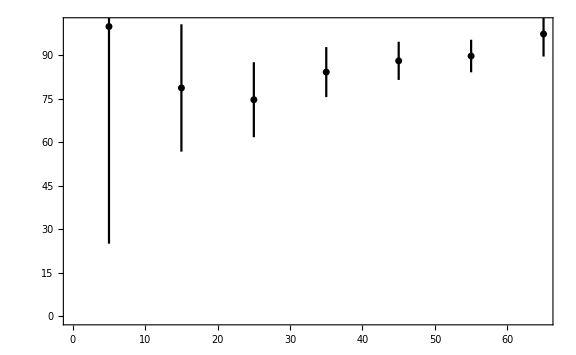

```mathematica
pllivefraction=ErrorListPlot[Transpose[{rshell,livefraction,sigma}],PlotRange->{-1,101},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Frazione di cellule vive in fase G1 (%) vs. distanza da centroide (µm)

```mathematica
G1inShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]==1  || phase[[maxstep,k]]==2,G1inShell[[shell[[k]]]]++ ];
k++];
For[k=1,k≤nshellmax,
If[G1inShell[[k]]>0,
G1inShell[[k]]=100.*G1inShell[[k]]/liveinShell[[k]];
sigma[[k]] = 100.*Sqrt[1/G1inShell[[k]]+1/liveinShell[[k]]]*(G1inShell[[k]]/liveinShell[[k]]),
G1inShell[[k]]=0;
sigma[[k]] = 0;];
k++];
```

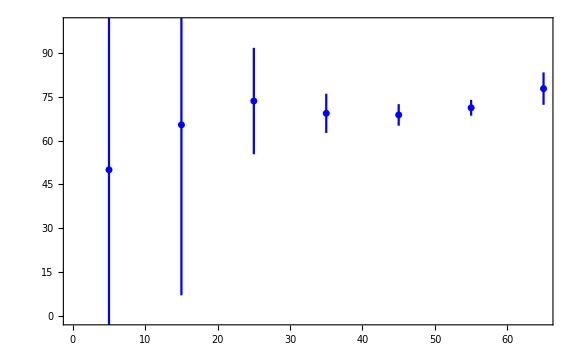

```mathematica
plG1fraction=ErrorListPlot[Transpose[{rshell,G1inShell,sigma}],PlotRange->{-1,100},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Blue,AbsolutePointSize[5]]]
```

### Frazione di cellule in fase G2 (%) vs. distanza da centroide (µm)

```mathematica
G2inShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]==4,G2inShell[[shell[[k]]]]++ ];
k++];
For[k=1,k≤nshellmax,
If[G2inShell[[k]]>0,
G2inShell[[k]]=100.*G2inShell[[k]]/liveinShell[[k]];
sigma[[k]] = 100.*Sqrt[1/G2inShell[[k]]+1/liveinShell[[k]]]*(G2inShell[[k]]/liveinShell[[k]]),
G2inShell[[k]]=0;
sigma[[k]] = 0;];
k++];
```

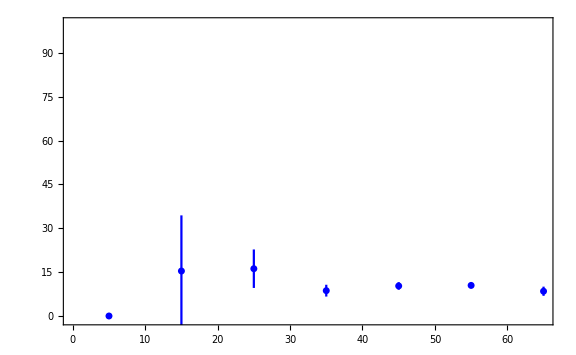

```mathematica
plG2fraction=ErrorListPlot[Transpose[{rshell,G2inShell,sigma}],PlotRange->{-1,100},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Blue,AbsolutePointSize[5]]]
```

### Frazione di cellule vive in fase S (%) vs. distanza da centroide (µm)

```mathematica
SinShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]==3,SinShell[[shell[[k]]]]++ ];
k++];
For[k=1,k≤nshellmax,
If[SinShell[[k]]>0,
SinShell[[k]]=100.*SinShell[[k]]/liveinShell[[k]];
sigma[[k]] = 100.*Sqrt[1/SinShell[[k]]+1/liveinShell[[k]]]*(SinShell[[k]]/liveinShell[[k]]),
SinShell[[k]]=0;
sigma[[k]] = 0;];
k++];
```

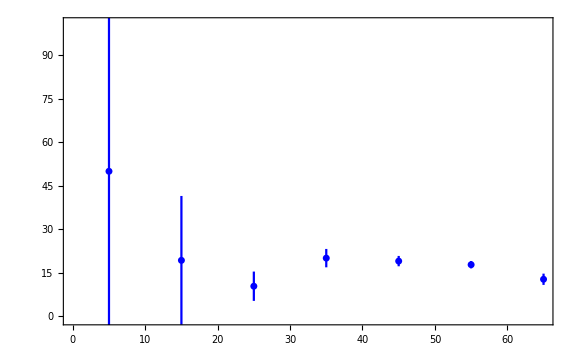

```mathematica
plSfraction=ErrorListPlot[Transpose[{rshell,SinShell,sigma}],PlotRange->{-1,101},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Blue,AbsolutePointSize[5]]]
```

### Frazione di cellule vive in fase M (%) vs. distanza dal centroide (µm)

```mathematica
MinShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]==5,MinShell[[shell[[k]]]]++ ];
k++];
For[k=1,k≤nshellmax,
If[MinShell[[k]]>0,
MinShell[[k]]=100.*MinShell[[k]]/liveinShell[[k]];
sigma[[k]] = 100.*Sqrt[1/MinShell[[k]]+1/liveinShell[[k]]]*(MinShell[[k]]/liveinShell[[k]]),
MinShell[[k]]=0;
sigma[[k]] = 0;];
k++];
```

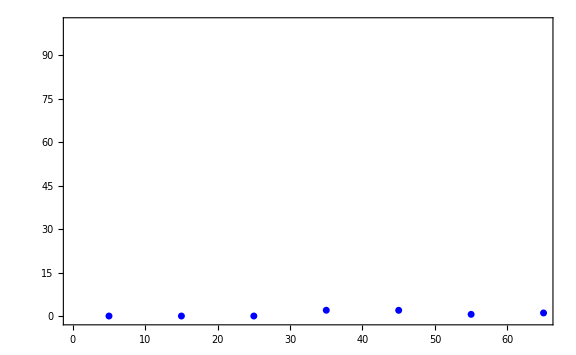

```mathematica
plMfraction=ErrorListPlot[Transpose[{rshell,MinShell,sigma}],PlotRange->{-1,101},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Blue,AbsolutePointSize[5]]]
```

### Frazione di cellule in proliferativa (S+G2+M, %) vs. distanza dal centroide (µm)

```mathematica
prolifinShell =Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
If[phase[[maxstep,k]]== 3 || phase[[maxstep,k]]==4 || phase[[maxstep,k]]==5,prolifinShell[[shell[[k]]]]++ ];
k++];
For[k=1,k≤nshellmax,
If[prolifinShell[[k]]>0,
prolifinShell[[k]]=100.*prolifinShell[[k]]/liveinShell[[k]];
sigma[[k]] = 100.*Sqrt[1/prolifinShell[[k]]+1/liveinShell[[k]]]*(prolifinShell[[k]]/liveinShell[[k]]),
prolifinShell[[k]]=0;
sigma[[k]] = 0;];
k++];
```

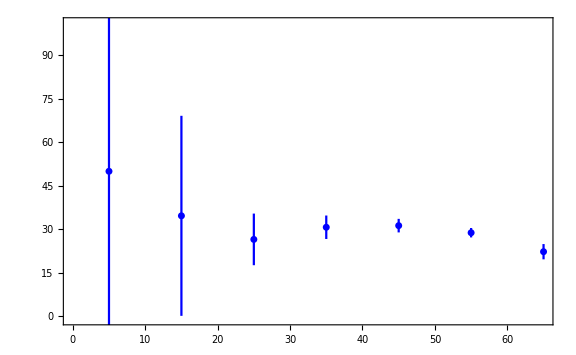

```mathematica
plproliffraction=ErrorListPlot[Transpose[{rshell,prolifinShell,sigma}],PlotRange->{-1,101},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Blue,AbsolutePointSize[5]]]
```

### Connettività delle cellule morte vs. distanza dal centroide (µm)

```mathematica
deadinShell =Table[0,{nshellmax}];
countinShell=count2inShell = Table[0,{nshellmax}];

For[k=1,k≤ncells[[maxstep]],
deadneighbors=Count[phase[[maxstep,links[[maxstep,k]]]],6];
If[phase[[maxstep,k]]==6,deadinShell[[shell[[k]]]]++;countinShell[[shell[[k]]]] += deadneighbors; count2inShell[[shell[[k]]]] += deadneighbors^2 ];
k++];
averageCount = Table[If[deadinShell [[n]]>0,countinShell[[n]]/deadinShell [[n]],0],{n,1,nshellmax}];
sdCount =  Table[If[deadinShell [[n]]>0,Sqrt[( count2inShell[[n]]/deadinShell [[n]] - averageCount[[n]]^2)/deadinShell [[n]] ],0],{n,1,nshellmax}];
```

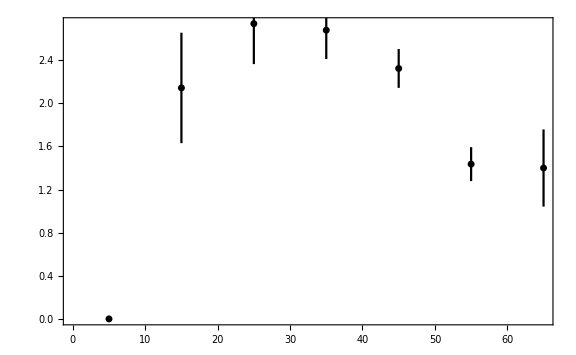

```mathematica
pldeadneighborcount=ErrorListPlot[Transpose[{rshell,averageCount, sdCount}],Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Velocità media (media del modulo, µm/s) vs. distanza dal centroide (µm)

```mathematica
vShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
vShell[[shell[[k]]]]+= Norm[v[[maxstep,k]]];
k++];
va=Table[If[nshell[[k]]>0,vShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
vamin= Min[va];
vamax= Max[va];
```

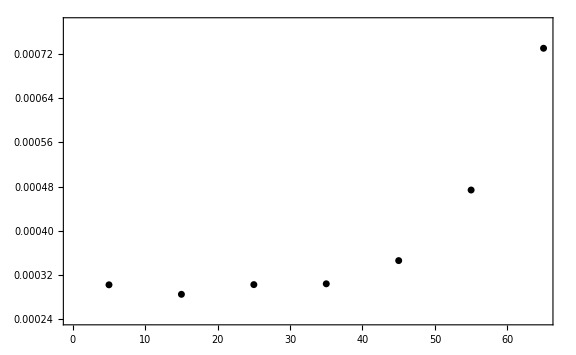

```mathematica
plva=ListPlot[Transpose[{rshell,va}],PlotRange->{vamin-0.1(vamax-vamin),vamax+0.1(vamax-vamin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Velocità radiale (µm/s) vs. distanza dal centroide (µm)

```mathematica
vrShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
versor = (x[[maxstep,k]]-ct[[maxstep]])/Norm[(x[[maxstep,k]]-ct[[maxstep]])];
vrShell[[shell[[k]]]]+= v[[maxstep,k]].versor;
k++];
vr=Table[If[nshell[[k]]>0,vrShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
vrmin= Min[vr];
vrmax= Max[vr];
```

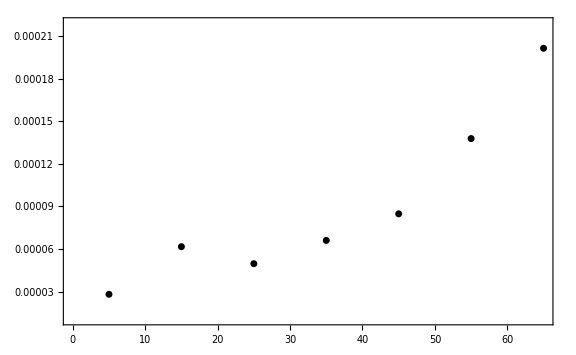

```mathematica
plvra=ListPlot[Transpose[{rshell,vr}],PlotRange->{vrmin-0.1(vrmax-vrmin),vrmax+0.1(vrmax-vrmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->True,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso medio dell'O2 (media del modulo, kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fO2Shell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
fO2Shell[[shell[[k]]]]+= Norm[fO2[[maxstep,k]]];
k++];
fO2a=Table[If[nshell[[k]]>0,fO2Shell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fO2amin= Min[fO2a];
fO2amax= Max[fO2a];
```

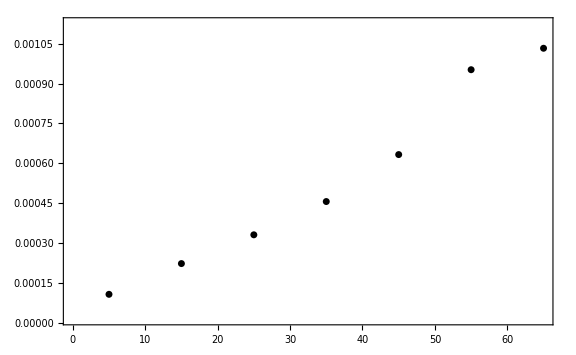

```mathematica
plfO2a=ListPlot[Transpose[{rshell,fO2a}],PlotRange->{fO2amin-0.1(fO2amax-fO2amin),fO2amax+0.1(fO2amax-fO2amin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso radiale medio di O2 (kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fO2rShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
versor = (x[[maxstep,k]]-ct[[maxstep]])/Norm[(x[[maxstep,k]]-ct[[maxstep]])];
fO2rShell[[shell[[k]]]]+= fO2[[maxstep,k]].versor;
k++];
fO2r=Table[If[nshell[[k]]>0,fO2rShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fO2rmin= Min[fO2r];
fO2rmax= Max[fO2r];
```

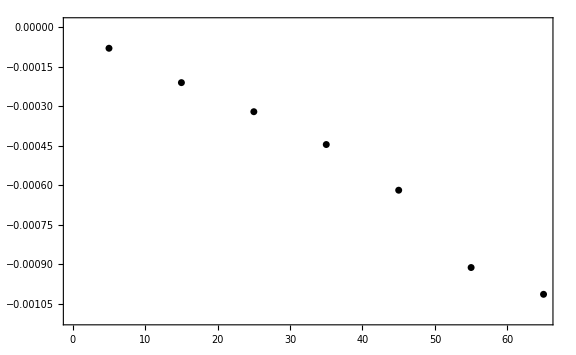

```mathematica
plfO2r=ListPlot[Transpose[{rshell,fO2r}],PlotRange->{fO2rmin-0.1(fO2rmax-fO2rmin),fO2rmax+0.1(fO2rmax-fO2rmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->True,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso medio del glucosio extracellulare (media del modulo, kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fGShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
fGShell[[shell[[k]]]]+= Norm[fG[[maxstep,k]]];
k++];
fGa=Table[If[nshell[[k]]>0,fGShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fGamin= Min[fGa];
fGamax= Max[fGa];
```

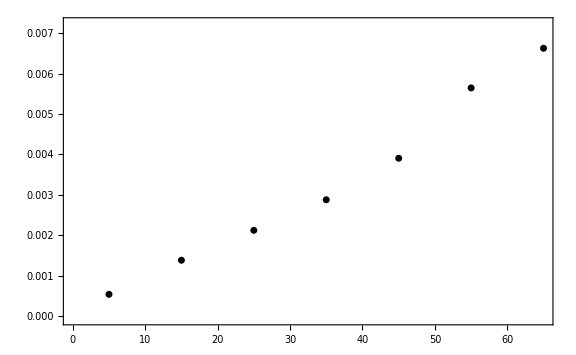

```mathematica
plfGa=ListPlot[Transpose[{rshell,fGa}],PlotRange->{fGamin-0.1(fGamax-fGamin),fGamax+0.1(fGamax-fGamin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso radiale medio del glucosio extracellulare (kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fGrShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
versor = (x[[maxstep,k]]-ct[[maxstep]])/Norm[(x[[maxstep,k]]-ct[[maxstep]])];
fGrShell[[shell[[k]]]]+= fG[[maxstep,k]].versor;
k++];
fGr=Table[If[nshell[[k]]>0,fGrShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fGrmin= Min[fGr];
fGrmax= Max[fGr];
```

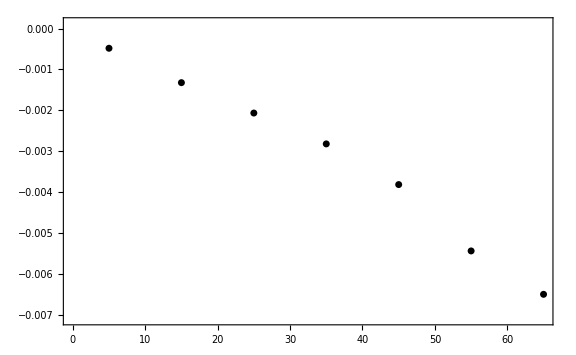

```mathematica
plfGr=ListPlot[Transpose[{rshell,fGr}],PlotRange->{fGrmin-0.1(fGrmax-fGrmin),fGrmax+0.1(fGrmax-fGrmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->True,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso medio della glutammina extracellulare (media del modulo, kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fAShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
fAShell[[shell[[k]]]]+= Norm[fA[[maxstep,k]]];
k++];
fAa=Table[If[nshell[[k]]>0,fAShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fAamin= Min[fAa];
fAamax= Max[fAa];
```

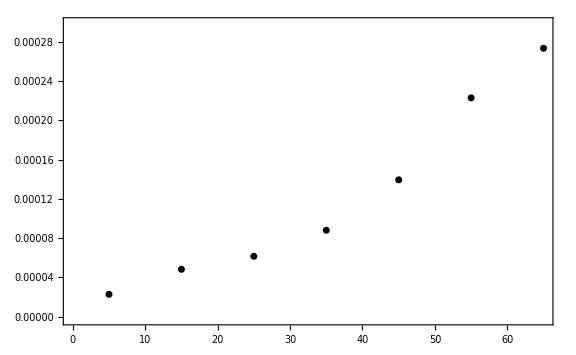

```mathematica
plfAa=ListPlot[Transpose[{rshell,fAa}],PlotRange->{fAamin-0.1(fAamax-fAamin),fAamax+0.1(fAamax-fAamin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso radiale medio della glutammina extracellulare (kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fArShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
versor = (x[[maxstep,k]]-ct[[maxstep]])/Norm[(x[[maxstep,k]]-ct[[maxstep]])];
fArShell[[shell[[k]]]]+= fA[[maxstep,k]].versor;
k++];
fAr=Table[If[nshell[[k]]>0,fArShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fArmin= Min[fAr];
fArmax= Max[fAr];
```

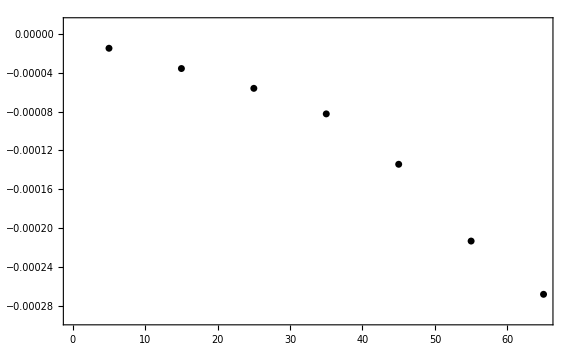

```mathematica
plfAr=ListPlot[Transpose[{rshell,fAr}],PlotRange->{fArmin-0.1(fArmax-fArmin),fArmax+0.1(fArmax-fArmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->True,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso medio dell'acido lattico extracellulare (media del modulo, kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fAcLShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
fAcLShell[[shell[[k]]]]+= Norm[fAcL[[maxstep,k]]];
k++];
fAcLa=Table[If[nshell[[k]]>0,fAcLShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fAcLamin= Min[fAcLa];
fAcLamax= Max[fAcLa];
```

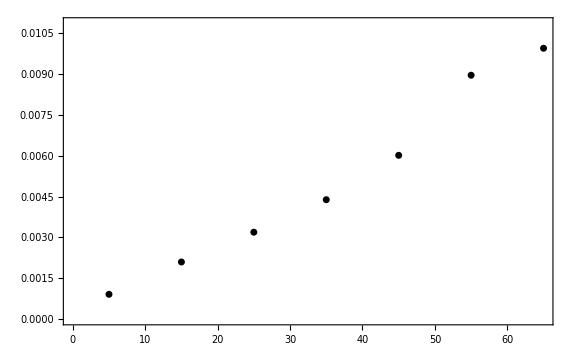

```mathematica
plfAcLa=ListPlot[Transpose[{rshell,fAcLa}],PlotRange->{fAcLamin-0.1(fAcLamax-fAcLamin),fAcLamax+0.1(fAcLamax-fAcLamin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->False,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```

### Flusso radiale medio dell'acido lattico extracellulare (kg/s/cellula) vs. distanza dal centroide (µm)

```mathematica
fAcLrShell= Table[0,{nshellmax}];
For[k=1,k≤ncells[[maxstep]],
versor = (x[[maxstep,k]]-ct[[maxstep]])/Norm[(x[[maxstep,k]]-ct[[maxstep]])];
fAcLrShell[[shell[[k]]]]+= fAcL[[maxstep,k]].versor;
k++];
fAcLr=Table[If[nshell[[k]]>0,fAcLrShell[[k]]/nshell[[k]],0],{k,1,nshellmax}];
fAcLrmin= Min[fAcLr];
fAcLrmax= Max[fAcLr];
```

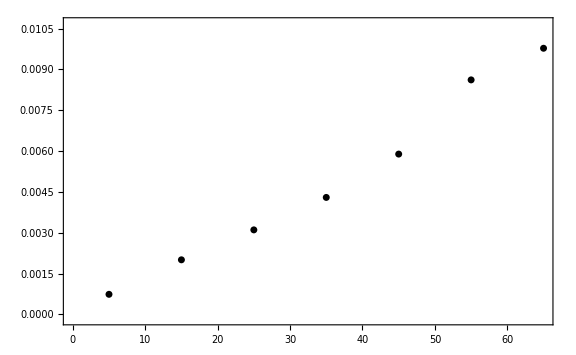

```mathematica
plfAcLr=ListPlot[Transpose[{rshell,fAcLr}],PlotRange->{fAcLrmin-0.1(fAcLrmax-fAcLrmin),fAcLrmax+0.1(fAcLrmax-fAcLrmin)},Frame->True,FrameStyle->18,ImageSize->8*72,Axes->True,PlotStyle->Directive[Black,AbsolutePointSize[5]]]
```